# top26Pc-cited articles (top25~26%)

## 環境設定

```mathematica
(*expordoctdir="/Users/kouamano/gitsrc/pubmed-analysis/202312/"*)
```

```mathematica
expordoctdir="/Volumes/LaCie/BANK/pubmed-analysis/202312/"
```

/Volumes/LaCie/BANK/pubmed-analysis/202312/

## 登録論文数累積

のちの分析のため評価必要。

edgestat-refcount-cumulative.nb より。

```mathematica
artcountAcm={331362,866254,1415896,2141764,3156527,4323230,5675522,7217673,9135438,11279956,13673661,16645203,20421796,25376280,31440632}
```

{331362,866254,1415896,2141764,3156527,4323230,5675522,7217673,9135438,11279956,13673661,16645203,20421796,25376280,31440632}

## 累積世代ごとの高被引用論文(G2)

のちの分析のため評価必要。

### G2論文

```mathematica
top26Pcartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt26Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt26Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt26Perc.save}

```mathematica
Map[Get,top26Pcartfiles];
```

主要論文PMIDと被引用数

```mathematica
(top26PcCitedArtList=Table[Reverse[SortBy[Flatten[Map[#[[2]]&,topCitingCitedArt26Perc[n,"citing rule"],{2}]]//Tally,#[[2]]&]],{n,1950,2020,5}])//Length
```

15

```mathematica
Map[#[[2]]&,top26PcCitedArtList,{2}]//Max
Map[#[[2]]&,top26PcCitedArtList,{2}]//Min
```

91

4

全期間のユニークPMID

```mathematica
(top26PcCitedArtPMID=Map[#[[1]]&,top26PcCitedArtList,{2}]//Flatten//Union)//Length
```

89021

```mathematica
numG2=Length[top26PcCitedArtPMID]
```

89021

高被引用論文数

```mathematica
top26PcCitedArtCount=Map[Length,top26PcCitedArtList]
```

{76,305,618,937,1449,2056,2835,3668,4663,5933,7239,9779,14655,19457,25231}

全論文数における高被引用論文数割合（%）

```mathematica
top26pcArtRatio=top26PcCitedArtCount/artcountAcm*100//N
```

{0.0229356,0.0352091,0.0436473,0.043749,0.0459049,0.047557,0.0499514,0.0508197,0.051043,0.0525977,0.0529412,0.0587497,0.0717616,0.076674,0.0802497}

## （調査１）高被引用(G2)論文タイトル

PMIDから論文タイトルを引くルール

プログラム適応

```mathematica
(*(blks=FileNames["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/*blk"])//Length*)
```

```mathematica
(*AbsoluteTiming[(pmidToTitle=Association[Flatten[ParallelMap[blkToTitleRule,blks]]]);]*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save",pmidToTitle]*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle_V2.save",pmidToTitle]*)
```

G2論文タイトル

ルールを読み込む

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save"];*)
```

```mathematica
(*top26pctitle=Map[{pmidToTitle[#[[1]]],#[[2]]}&,top26PcCitedArtList,{2}];*)
```

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top26pctitle.save",top26pctitle]*)
```

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"top26pctitle.save"];
```

## （調査２.１）G2論文のオブソレッセンス（全ての累積世代での出現）

全累積世代に見る論文を候補とする。

```mathematica
top26PcCitedArtPMID//Length
```

89021

### pubyearを調べておく

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/PMIDtoPubyear.wl"];
```

```mathematica
top26PcCitingCitedPMIDvsPY=Map[{#,PMIDtoPubyear[#]}&,top26PcCitedArtPMID];
```

```mathematica
yearlist=Sort[Tally[Map[#[[2]]&,top26PcCitingCitedPMIDvsPY]]]
```

{{1880,1},{1886,1},{1889,1},{1890,1},{1894,3},{1895,1},{1898,2},{1899,1},{1900,1},{1905,1},{1907,1},{1908,1},{1912,2},{1913,5},{1914,2},{1915,3},{1916,3},{1917,3},{1918,1},{1919,3},{1920,2},{1921,5},{1922,2},{1923,5},{1924,3},{1925,5},{1926,6},{1927,7},{1928,8},{1929,10},{1930,5},{1931,15},{1932,21},{1933,24},{1934,21},{1935,20},{1936,21},{1937,29},{1938,35},{1939,30},{1940,38},{1941,51},{1942,48},{1943,55},{1944,64},{1945,98},{1946,106},{1947,107},{1948,125},{1949,188},{1950,414},{1951,569},{1952,523},{1953,526},{1954,487},{1955,539},{1956,612},{1957,633},{1958,754},{1959,667},{1960,605},{1961,601},{1962,641},{1963,663},{1964,722},{1965,656},{1966,722},{1967,698},{1968,809},{1969,812},{1970,900},{1971,894},{1972,885},{1973,841},{1974,995},{1975,1061},{1976,1081},{1977,1133},{1978,1037},{1979,1010},{1980,1033},{1981,1078},{1982,1189},{1983,1159},{1984,1294},{1985,1277},{1986,1336},{1987,1385},{1988,1492},{1989,1519},{1990,1702},{1991,1684},{1992,1789},{1993,1796},{1994,1751},{1995,1832},{1996,1823},{1997,1875},{1998,2085},{1999,2132},{2000,2318},{2001,2337},{2002,2392},{2003,2429},{2004,2604},{2005,2680},{2006,2530},{2007,2467},{2008,2496},{2009,2274},{2010,2224},{2011,1927},{2012,1540},{2013,1240},{2014,945},{2015,637},{2016,494},{2017,306},{2018,162},{2019,51},{2020,55},{2021,1}}

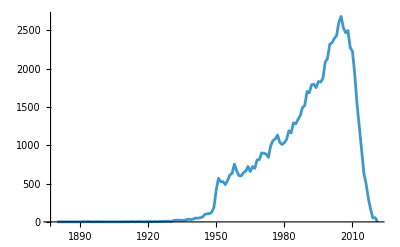

```mathematica
ListPlot[yearlist//ToExpression,PlotRange->Full,Joined->True]
```

### あらためて各論文の被引用の状況を確認する

```mathematica
Map[#[[1]]&,yearlist]//ToExpression//Max
Map[#[[1]]&,yearlist]//ToExpression//Min
```

2021

1880

最も古い高被引用論文は1880出版。

```mathematica
targetYears=Table[ToString[n],{n,1880,2020}]
```

{1880,1881,1882,1883,1884,1885,1886,1887,1888,1889,1890,1891,1892,1893,1894,1895,1896,1897,1898,1899,1900,1901,1902,1903,1904,1905,1906,1907,1908,1909,1910,1911,1912,1913,1914,1915,1916,1917,1918,1919,1920,1921,1922,1923,1924,1925,1926,1927,1928,1929,1930,1931,1932,1933,1934,1935,1936,1937,1938,1939,1940,1941,1942,1943,1944,1945,1946,1947,1948,1949,1950,1951,1952,1953,1954,1955,1956,1957,1958,1959,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020}

```mathematica
(G2targetCandPMIDvsPY=Map[{#,PMIDtoPubyear[#]}&,top26PcCitedArtPMID])//Length
```

89021

PMIDからタイトルを引く

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"pmidToTitle.save"];*)
```

```mathematica
(*(G2targetCandPMIDvsTitle=Map[{#,pmidToTitle[#]}&,top26PcCitedArtPMID])//Length*)
```

89021

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"G2targetCandPMIDvsTitle.save",G2targetCandPMIDvsTitle]*)
```

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/title/"<>"G2targetCandPMIDvsTitle.save"];*)
```

PMID vs. PMID

```mathematica
(*Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/totalEdge.save"];*)
```

```mathematica
(*AbsoluteTiming[totalEdgeGroupLast=GroupBy[totalEdgeList,Last];]*)
```

{234.077,Null}

```mathematica
(*AbsoluteTiming[(top26PcCitedArtEdges=Map[totalEdgeGroupLast,top26PcCitedArtPMID])//Length]*)
```

{0.568145,89021}

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/top26PcCitedArtEdges.save",top26PcCitedArtEdges]*)
```

以下はデータ整形

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/top26PcCitedArtEdges.save"];
```

```mathematica
(top26PcCitedArtCitedyear= Map[{PMIDtoPubyear[#[[1]]],{PMIDtoPubyear[#[[2]]],#[[2]]}}&, top26PcCitedArtEdges,{2}])//Length
```

89021

yearごとの被引用数リストを作る

：yearから被引用数を得る

```mathematica
toCitedyearlist[l_]:=Module[{citedPMID},
citedPMID=l[[1,2]];
{citedPMID,Association[MapApply[Rule,Tally[Map[#[[1]]&,l]]]]}
]
```

```mathematica
(top26PcCitedArtCitedyearAssociations=Map[toCitedyearlist,top26PcCitedArtCitedyear])//Length
```

89021

：1880からの被引用数リストにする

```mathematica
fromAscToCount[asc_,year_]:=Map[asc[#]&,year]/.{_Missing->0}
```

<1880からの累積被引用数リスト>

```mathematica
(top26PcCitedArtCitedCount["1880-2020"]=Map[{#[[1]],fromAscToCount[#[[2]],targetYears]}&,top26PcCitedArtCitedyearAssociations])//Length
```

89021

：出版年からの被引用数リストにする

```mathematica
fromPY[l_,y_]:=Module[{py,pyp},
py=l[[1,1]];
pyp=Flatten[Position[y,py]][[1]];
{l[[1]],l[[2]][[pyp;;]]}
]
```

```mathematica
(top26PcCitedArtCitedCount["PY-2020"]=Map[fromPY[#,targetYears]&,top26PcCitedArtCitedCount["1880-2020"]])//Length
```

Part::partw: {}の部分1は存在しません．

Part::span: {}⟦1⟧;;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

89021

### 分析

#### plot用カラー/サイズ定義

以下はplotの色の調整

```mathematica
myColor1[z_]:=RGBColor[z,0.8(1-z),0.4(1-z)];
myColor2[z_]:=CMYKColor[z,((1-z)/3)^2,((1-z)/2)^2,Sqrt[z]];
myColor3[z_]:=CMYKColor[((1-z)/3)^2,z,((1-z)/2)^2,Sqrt[z]];
myColor4[z_]:=CMYKColor[((1-z)/3)^2,((1-z)/3)^2,z,Sqrt[z]];
myColor5[z_]:=CMYKColor[(z)^2,(z),(z),(z)^(1.2)];
myColor6[z_]:=Blend[{Red,Green,White},{1,0.75(1-z),(1-z)^(3)}];
cf1=Function[{x,y,z},Hue[5/6 (1-z),0.3+(z^2),1]];
cf2=Function[{x,y,z},Hue[5/6 (1-z),#+(1-#)*z,1]&@0.05];
cf3=Function[{x,y,z},Hue[5/6*(1-z),(#1+(1-#1)*z)^#2,1]]&@@{.25(*offset*),1.0(*gain*)};
```

```mathematica
imsz1=260
imsz2=320
imsz3=480
imsz4=540
```

260

320

480

540

#### 指標値

オブソレッセンスベクトル = O(Gs,A-)：Sunらの論文より、指標 "Gs" と "A-" の定義：
Gs = 1 - ((2 [n*c1 + (n-1)*c2 + ...] - C) / (C*n)); n:age, c:year cited, C:total cited;
A = “A-” + “A+”;
B : year accumulation (normarized).
"A-"、"A+"にかかる定義文（和訳）:「したがって、値が正となる A+ を、平等線（完全平等線）と、その平等線より下にある正規化曲線との間の面積として定義し、値が負となる A− を、平等線と、その平等線より上にある正規化曲線との間の面積として定義する。」
このとき、オブソレッセンスベクトルは : (Gs,”A-”)

```mathematica
Gsf[l_]:=Module[{len,Ct,Yr},
len=Length[l];
Ct=Total[l];
Yr=Reverse[Table[n,{n,Length[l]}]];
If[Ct==0,1,1-((2 Total[Yr * l]-Ct) / (len * Ct))]
]
```

```mathematica
obsGs[l_]:=Module[{ac,acR,ht,len,area,A,Gs,Ang,Ap,normstep,normseq,Aseq},
ac=Accumulate[l]//N;
ht=Last[ac];
len=Length[ac];
area=ht*len;
acR=ac/area;
normstep=Last[acR]/len;
normseq=Table[normstep*n,{n,len}];
Aseq=normseq-acR;
A=Total[Aseq];
Ang=Cases[Aseq,x_/;x<0]//Total;
Ap=Cases[Aseq,x_/;x>0]//Total;
Gs=Gsf[l]//N;
Association[{"Gs"->Gs,"A-"->Ang,"A+"->Ap,"A"->A,"len"->len}]
]
```

```mathematica
obsGsseq[l_]:=Table[obsGs[Take[l,n]],{n,Length[l]}]
```

その他の主要指標：

"len" => 出版から2020までの年数
“peakYear” => 出版からピークを迎えるまでの年数☑️
“peakCount” => ピークの年の被引用数☑️
“peakRatio” => peakCount/decayCited（”活動期間”の被引用）
“peakPosition” => “活動期間”中におけるpeakの位置（全体を1とする）
“sustainYear” => ピークの年から2020までの年数
“acR” => last cited / accumulate cited
“decayYear” => ピークの年を超えてから年間引用が全体の引用の5%以下となるまでの出版からの年数☑️
“decayCited” => decayYearまでの被引用数☑️
“firstCitedYear” => 最初の引用が発生するまでの年数（出版年に発生すると0）
“totalCited” => 出版年から2020までの総被引用数
“V:Av5year” => 5年引用数平均の分散☑️
“V:diff” => 5年引用数平均の差分の分散（ゼロパディングあり=>出版年での立ち上がりが見える）☑️
“V:diff2” => 5年引用数平均の差分の差分の分散☑️
“diffTotal” => 5年引用数平均の差分の累計：十分に大きい値があり十分に長い期間があれば0に近づく

```mathematica
acRatio[l_]:=Module[{ac},
ac=Accumulate[l];
N[l/ac]/.Indeterminate->1
]
```

```mathematica
ndiff[l_,w_]:=BlockMap[(#[[-1]]-#[[1]])/(w-1)&,Join[Table[0,{w-1}],l],w,1]
```

```mathematica
ndiff[l_]:=BlockMap[(#[[-1]]-#[[1]])&,l,2,1]
```

```mathematica
myVar[l_]:=If[Length[l]>1,Variance[l],0]
```

```mathematica
basicStat[citedcount_]:=Module[{len,argPeak,peakYear,max,sustainYear,decayTH,acR,decayPlist,decayCited,decayPeriod,firstCitedYear,total,Av5year,diff,diff2,diffTotal},
decayTH=0.05;
len=Length[citedcount];
argPeak=Flatten[Position[citedcount,max=Max[citedcount]]];
peakYear=argPeak[[1]];
sustainYear=len-argPeak[[-1]];
acR=acRatio[citedcount];
decayPlist=Cases[Flatten[Position[acRatio[citedcount],x_/;x<=decayTH]],x_/;x>peakYear];
decayCited=Total[citedcount[[;;Min[decayPlist]]]];
decayPeriod=Min[decayPlist]-peakYear;
If[Length[decayPlist]<=0,decayPeriod="InDecay"];
firstCitedYear=Min[Position[citedcount,x_/;x>0]]-1;
total=Total[citedcount];
Av5year=MovingAverage[Join[citedcount,Table[0,{n,4}]],5];
diff=ndiff[Av5year];
diff2=ndiff[diff];
diffTotal=Total[diff//N];
Association[{"len"->len,"peakYear"->peakYear,"peakCount"->max,"peakRatio"->max/decayCited//N,"acRatio"->acR,"peakPosition"->peakYear/Min[decayPlist]//N,"sustainYear"->sustainYear,"decayCited"->decayCited,"decayPeriod"->decayPeriod,"firstCitedYear"->firstCitedYear,"totalCited"->total,"V:Av5year"->myVar[Av5year//N],"V:diff"->myVar[diff//N],"V:diff2"->myVar[diff2//N],"diffTotal"->diffTotal,"diffSeq"->diff}]
]
```

```mathematica
toItemNormarizeMat[l_]:=Module[{m,key},
key=Keys[l[[1,2]]];
m=Map[Normal[#[[2]]]&,l]/.{None->0};
Transpose[Map[Normalize,Transpose[Map[#[[2]]&,m,{2}]]]//N]
]
```

```mathematica
totalize[l_]:=l/Total[l]
```

```mathematica
(G2bs=Map[{#[[1]],basicStat[#[[2]]]}&,top26PcCitedArtCitedCount["PY-2020"]])//Length
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

Power::infy: 無限式1/0が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

Part::span: 1;;∞は有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

General::stop: この計算中に，Part::spanのこれ以上の出力は表示されません．

Part::partw: {}の部分1は存在しません．

Part::partw: {}の部分-1は存在しません．

Part::pkspec1: 式{{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,«13»,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,«91»}は部分指定に使用できません．

Join::heads: 位置1と2での頭部PartとListは等しいことが想定されています．

MovingAverage::vecmat: 位置1の引数Join[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«91»}⟦{}⟦1⟧;;All⟧,{0,0,0,0}]が非空のベクトルでも非空の行列でもありません．

Join::heads: 位置1と2での頭部PartとListは等しいことが想定されています．

General::stop: この計算中に，Join::headsのこれ以上の出力は表示されません．

MovingAverage::vecmat: 位置1の引数Join[{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«91»}⟦{}⟦1⟧;;All⟧,{0.,0.,0.,0.}]が非空のベクトルでも非空の行列でもありません．

General::stop: この計算中に，MovingAverage::vecmatのこれ以上の出力は表示されません．

89021

```mathematica
(G2obsIdx=Map[obsGsseq[#[[2]]]&,top26PcCitedArtCitedCount["PY-2020"]])//Dimensions
```

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

Power::infy: 無限式1/0.が見付かりました．

Infinity::indet: 不定式0. ComplexInfinityが見付かりました．

General::stop: この計算中に，Infinity::indetのこれ以上の出力は表示されません．

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Part::span: {}⟦1⟧;;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

Part::pkspec1: 式{{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,«13»,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,{}⟦1⟧;;All,«91»}は部分指定に使用できません．

Thread::tdlen: {({0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«3»,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«91»}⟦{«1»}⟧)/(4 (89+Part[«2»];;All)),({0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«31»,0.,0.,0.,0.,0.,0.,0.,0.,0.,«91»}⟦{«1»}⟧)/(2 (89+Part[«2»];;All))}+{-({0.,0.,0.,«46»,0.,«91»}⟦{«1»}⟧)/(2 ({}⟦1⟧;;All)),-(«1»)/(2 «1»),«47»,-(«1»)/(«1»),«91»}の長さが異なるオブジェクトは結合することができません．

Part::span: {}⟦1⟧;;Allは有効なSpan指定ではありません．Span指定は;;で区切られた1個，2個，あるいは3個の機械サイズの整数でなければなりません（整数はどれも省略することができます．Allで置き換えることも可能です）．

{89021}

#### オブソレッセンスベクトルの確認

Sunらの論文の指標、O(Gs, A-)の算出。

```mathematica
Map[#["len"]&,Map[Last,G2obsIdx]]//Max
Map[#["len"]&,Map[Last,G2obsIdx]]//Min
```

141

1

```mathematica
(G2obsGs=Map[#["Gs"]&,Map[Last,G2obsIdx]])//Dimensions
(G2obsAng=Map[#["A-"]&,Map[Last,G2obsIdx]])//Dimensions
(G2obsAp=Map[#["A+"]&,Map[Last,G2obsIdx]])//Dimensions
(G2obsA=Map[{#["Gs"],#["A"]}&,Map[Last,G2obsIdx]])//Dimensions
(G2obsAA=Map[{#["A-"],#["A+"],#["Gs"]}&,Map[Last,G2obsIdx]])//Dimensions
(G2obsVec=Map[{#["Gs"],#["A-"]}&,Map[Last,G2obsIdx]])//Dimensions
(G2obsVecP=Map[{#["Gs"],#["A+"]}&,Map[Last,G2obsIdx]])//Dimensions
(G2obsSpec3D=Map[{#["Gs"],#["A-"],#["len"]}&,Map[Last[#]&,G2obsIdx]])//Dimensions
(G2obsA3D=Map[{#["A-"],#["A+"],#["len"]}&,Map[Last[#]&,G2obsIdx]])//Dimensions
```

{89021}

{89021}

{89021}

{89021,2}

{89021,3}

{89021,2}

{89021,2}

{89021,3}

{89021,3}

・引用ピークが早期であるほど "Gs" が小さくなる。
・オブソレッセンス状態にあるほど”A-”が小さくなる傾向にある。

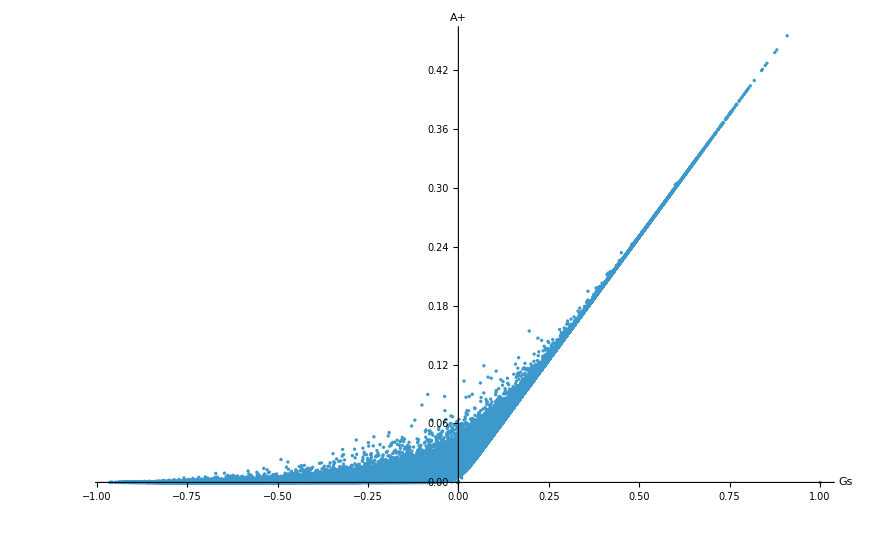

```mathematica
ListPlot[G2obsVecP,PlotRange->Full,AxesLabel->{Text[Style["Gs",20]],Text[Style["A+",20]]}]
```

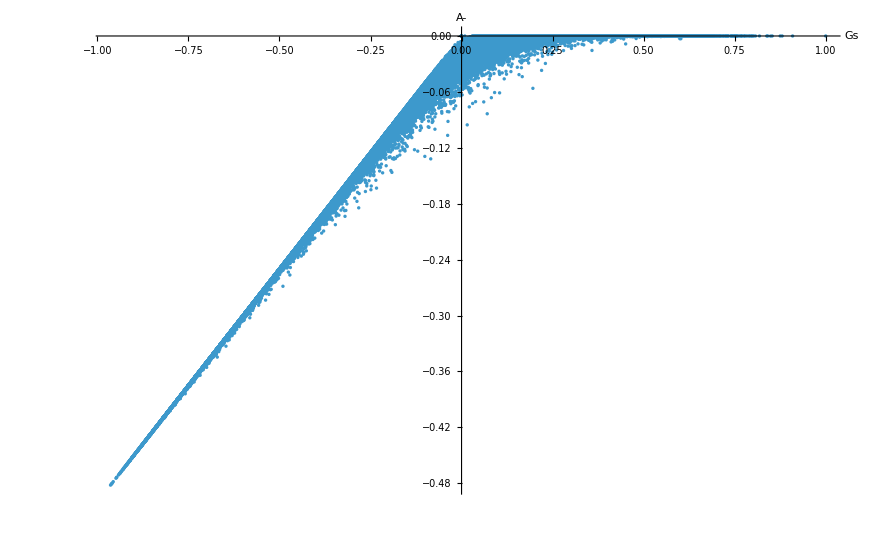

```mathematica
ListPlot[G2obsVec,PlotRange->Full,AxesLabel->{Text[Style["Gs",20]],Text[Style["A-",20]]}]
```

```mathematica
ListPointPlot3D[G2obsSpec3D,Filling->Bottom,AxesLabel->{"Gs","A-","year"}]
```

-Graphics3D-

#### Flash in the pan と Sleeping beauty、その他

Sunらの論文の指標、Gs、A- 、A+をを使い、Flash in the pan と Sleeping beauty の存在を確認する。

Paroloらの論文の報告 （ピーク年） とも比較する。（概ねどの分野も2~7年で被引用ピークを迎える）

```mathematica
binMaxPosition[l_,{min_,max_,step_}]:=Module[{span,BC,maxV,maxP},
span=Table[n,{n,min,max,step}];
BC=BinCounts[l,{min,max,step}];
maxV=Max[BC];
maxP=Position[BC,maxV]//Flatten;
(*{span,BC,maxV,maxP,{span[[maxP]],span[[maxP]]+step}};*)
{maxV,maxP,span[[maxP]],span[[maxP]]+step}
]
```

瓶幅：3

```mathematica
binW=3
```

3

FP; Flash in the pan

Gsが小さい Gs < -0.6

A-が小さい A- < - 0.3

```mathematica
(G2obsFP=Position[G2obsVec,{x_,y_}/;x<-0.6&&y<-0.3]//Flatten)//Length
```

11254

中央値：

```mathematica
G2medV["FP"]=G2obsAA[[G2obsFP]]//Median
```

{-0.347324,0.000287274,-0.69375}

```mathematica
G2len["FP"]=Map[#[[3]]&,G2obsA3D[[G2obsFP]]]//Median
```

51

Nm; 通常（対数正規分布）型

Gs: -0.6 <= Gs >= 0.6

A+の値を持つ: A+ > 0

A-の値を持つ: A- < 0

|A-| > |A+|

```mathematica
(G2obsNm=Position[G2obsAA,{ang_,ap_,gs_}/;gs>=-0.6&&gs<=0.6&&ang<0&&ap>0&&Abs[ang]>Abs[ap]]//Flatten)//Length
```

36575

中央値：

```mathematica
G2medV["Nm"]=G2obsAA[[G2obsNm]]//Median
```

{-0.119364,0.00242664,-0.231429}

```mathematica
G2len["Nm"]=Map[#[[3]]&,G2obsA3D[[G2obsNm]]]//Median
```

32

No; 通常型かつオブソレッセンス状態

Gs: -0.6 <= Gs >= 0.6

A+の値を持つ: A+ > 0

A-の値を持つ: A- < -0.1

|A-| > |A+|

```mathematica
(G2obsCmp=Position[G2obsAA,{ang_,ap_,gs_}/;gs>=-0.6&&gs<=0.6&&ang<-0.1&&ap>0&&Abs[ang]>Abs[ap]]//Flatten)//Length
```

20634

```mathematica
G2medV["No"]=G2obsAA[[G2obsCmp]]//Median
```

{-0.197542,0.00111111,-0.391667}

```mathematica
G2len["No"]=Map[#[[3]]&,G2obsA3D[[G2obsCmp]]]//Median//N
```

40.

SB; Sleeping beauty(1)

Gsが大きい Gs > 0.6

A+が大きい A+ > 0.3

```mathematica
(G2obsSB=Position[G2obsVecP,{x_,y_}/;x>0.6&&y>0.3]//Flatten)//Length
```

301

中央値：

```mathematica
G2medV["SB"]=G2obsAA[[G2obsSB]]//Median
```

{0,0.32381,0.647619}

```mathematica
G2len["SB"]=Map[#[[3]]&,G2obsA3D[[G2obsSB]]]//Median//N
```

42.

O; いずれにも分類されなかったもの

```mathematica
(G2obsOthers=Complement[Table[n,{n,numG2}],Join[G2obsFP,G2obsSB,G2obsNm]])//Length
```

40891

中央値：

```mathematica
G2medV["O"]=(G2obsAA[[G2obsOthers]]/.If[___]->0//Median)
```

If::argbu: Ifは1つの引数で呼ばれました．2個から4個の引数が想定されています．

{-0.000897989,0.0740741,0.14249}

```mathematica
G2len["O"]=Map[#[[3]]&,G2obsA3D[[G2obsOthers]]]//Median//N
```

19.

表：

項目

```mathematica
G2medV["head"]={"A^-","A^+","Gs"}
```

{A^-,A^+,Gs}

メンバー数

```mathematica
G2Nmem={11254,36575,20634,301,40891}
```

{11254,36575,20634,301,40891}

```mathematica
G2Pcmem=Round[G2Nmem/numG2*100]
```

{13,41,23,0,46}

年齢

```mathematica
G2Nlen={G2len["FP"],G2len["Nm"],G2len["No"],G2len["SB"],G2len["O"]}
```

{51,32,40.,42.,19.}

```mathematica
Append[Append[Prepend[Transpose[Prepend[Round[{G2medV["FP"],G2medV["Nm"],G2medV["No"],G2medV["SB"],G2medV["O"]},0.001],G2medV["head"]]],{"クラス","FP","Nm","No","SB","O"}],{"年齢",51.,32.,40.,42.,19.}],{"メンバー数\n(%:G1との比較)","11254(13↑)","36575(41↑)","20634(23↑)","301(0↓)","40891(46↓)"}]//Transpose//TableForm
```

クラス | A^- | A^+ | Gs | 年齢 | メンバー数
(%:G1との比較)
FP | -0.347 | 0. | -0.694 | 51. | 11254(13↑)
Nm | -0.119 | 0.002 | -0.231 | 32. | 36575(41↑)
No | -0.198 | 0.001 | -0.392 | 40. | 20634(23↑)
SB | 0. | 0.324 | 0.648 | 42. | 301(0↓)
O | -0.001 | 0.074 | 0.142 | 19. | 40891(46↓)

## かきなおしはここまで

PMID vs . クラス

```mathematica
PMIDtoobsClass=Association[{Map[#[[1,2]]->"FP"&,bs[[obsFP]]],Map[#[[1,2]]->"SB"&,bs[[obsSB]]],Map[#[[1,2]]->"N"&,bs[[obsNm]]],Map[#[[1,2]]->"O"&,bs[[obsOthers]]]}//Flatten];
```

クラスごとのベクトルプロット：

```mathematica
ListPointPlot3D[{obsAA[[obsFP]],obsAA[[obsSB]],obsAA[[obsNm]],obsAA[[obsOthers]]},Filling->Bottom,AxesLabel->{"A-","A+","Gs"},PlotRange->All,PlotLegends->{"FP","SB","Nm","O"}]
```

-Graphics3D-

#### オブソレッセンス条件の検討

total cited :

```mathematica
Map[#[[2]]["totalCited"]&,bs]//Max
Map[#[[2]]["totalCited"]&,bs]//Min
```

54249

51

```mathematica
1/54249//N
```

0.0000184335

```mathematica
1/51//N
```

0.0196078

acRatio :

```mathematica
Map[#[[2]]["acRatio"]&,bs]//ListLinePlot3D
```

-Graphics3D-

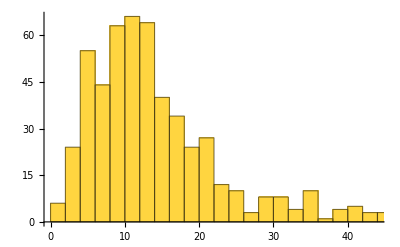

```mathematica
Histogram[Map[#[[2]]["peakYear"]&,bs],{2}]
```

```mathematica
Map[{#[[2]]["peakYear"],#[[2]]["len"]}&,bs]
```

{{25,25},{20,23},{17,22},{15,22},{30,31},{14,21},{21,21},{21,21},{16,21},{11,21},{14,21},{21,21},{15,21},{21,21},{19,21},{18,21},{19,21},{21,21},{10,46},{5,21},{19,20},{2,20},{14,20},{21,21},{12,20},{20,20},{15,20},{10,20},{17,20},{13,20},{4,20},{13,20},{12,20},{15,20},{20,20},{15,20},{12,46},{19,19},{7,46},{19,19},{12,19},{19,19},{20,20},{12,19},{14,19},{12,46},{17,19},{46,46},{19,19},{13,19},{19,19},{10,19},{12,19},{15,19},{11,19},{19,19},{18,19},{40,45},{3,19},{12,19},{19,19},{10,18},{14,18},{9,18},{12,18},{10,18},{12,18},{18,18},{10,18},{13,18},{18,18},{3,69},{4,69},{67,69},{4,69},{4,68},{4,68},{19,67},{5,67},{13,66},{18,66},{20,66},{13,66},{23,65},{12,65},{17,65},{65,65},{5,65},{64,64},{9,64},{16,63},{13,63},{4,63},{22,62},{62,62},{56,62},{62,62},{21,62},{14,62},{58,60},{60,60},{58,60},{10,60},{9,60},{11,61},{10,59},{5,58},{7,58},{10,58},{6,29},{21,58},{15,57},{7,56},{2,66},{8,66},{61,61},{23,59},{5,60},{5,60},{9,18},{18,18},{11,18},{12,17},{5,71},{21,71},{11,71},{20,70},{4,70},{13,70},{4,70},{8,70},{21,70},{5,70},{28,70},{7,43},{8,69},{17,69},{14,69},{63,69},{17,17},{17,17},{12,17},{13,17},{13,17},{17,17},{11,17},{8,17},{5,17},{17,17},{16,17},{5,16},{17,27},{14,24},{14,17},{11,72},{69,72},{12,71},{10,72},{3,72},{11,71},{16,72},{11,71},{24,71},{12,17},{15,17},{4,29},{8,17},{11,16},{16,16},{8,16},{16,16},{28,29},{16,16},{10,16},{16,16},{16,16},{8,16},{12,16},{16,16},{16,16},{16,16},{4,16},{15,15},{6,74},{5,15},{12,17},{72,72},{3,84},{13,83},{20,76},{10,76},{69,73},{24,88},{21,83},{20,81},{8,80},{15,79},{12,78},{11,78},{9,77},{12,76},{21,76},{5,74},{5,73},{4,73},{14,15},{9,15},{9,15},{12,15},{15,15},{9,15},{23,80},{9,72},{28,88},{15,15},{2,14},{75,78},{5,76},{6,14},{13,14},{14,14},{5,14},{6,14},{3,14},{14,14},{30,30},{9,14},{9,14},{14,14},{14,14},{13,14},{3,75},{4,73},{7,14},{14,14},{30,30},{6,14},{3,76},{6,14},{9,14},{35,72},{4,13},{10,13},{2,13},{7,13},{8,13},{8,13},{5,30},{13,13},{13,13},{13,13},{6,13},{13,13},{40,42},{12,12},{7,12},{13,13},{12,12},{12,12},{13,13},{12,12},{9,12},{4,12},{12,12},{9,12},{9,12},{6,14},{26,30},{10,12},{12,12},{12,12},{12,12},{11,14},{2,12},{11,12},{11,11},{12,12},{29,29},{12,12},{12,12},{12,12},{11,12},{12,12},{4,12},{11,11},{8,12},{12,12},{10,11},{11,11},{11,11},{11,11},{10,11},{17,30},{7,11},{11,11},{10,11},{8,11},{11,11},{11,11},{7,11},{11,11},{3,11},{11,11},{10,11},{8,11},{4,11},{10,10},{5,10},{5,11},{10,10},{10,10},{7,10},{4,10},{9,10},{8,10},{10,10},{29,31},{8,10},{10,10},{4,31},{10,10},{2,9},{31,31},{9,9},{7,9},{9,9},{9,9},{9,9},{8,9},{9,9},{6,9},{9,9},{9,9},{9,9},{9,9},{7,9},{5,9},{8,8},{4,9},{8,8},{6,9},{5,8},{8,8},{2,8},{8,8},{5,8},{10,46},{4,8},{8,8},{8,34},{2,7},{10,34},{7,7},{4,33},{10,34},{7,7},{16,23},{31,32},{5,6},{6,6},{7,7},{6,6},{2,6},{6,6},{6,6},{4,6},{6,6},{5,6},{5,44},{8,32},{2,5},{4,5},{5,5},{4,5},{15,44},{21,32},{32,32},{4,5},{17,24},{2,4},{36,36},{35,35},{6,42},{2,3},{7,36},{6,36},{3,3},{7,33},{2,2},{6,33},{1,1},{1,1},{1,1},{8,44},{33,33},{1,1},{1,1},{1,1},{10,44},{8,34},{27,34},{25,33},{28,33},{33,33},{8,44},{34,34},{8,35},{34,34},{34,34},{9,34},{42,42},{18,34},{11,35},{28,34},{29,35},{35,35},{10,36},{35,36},{8,36},{10,42},{11,42},{31,36},{34,36},{14,53},{40,48},{20,54},{11,50},{43,49},{43,47},{16,49},{47,49},{18,47},{18,48},{10,47},{12,52},{23,52},{12,56},{44,50},{11,42},{23,51},{47,53},{9,52},{15,55},{19,55},{14,44},{5,37},{6,41},{12,40},{7,38},{3,37},{8,37},{6,41},{35,41},{6,41},{7,40},{5,40},{14,40},{6,39},{5,39},{4,39},{6,38},{11,38},{8,38},{9,37},{7,37},{12,39},{10,38},{9,38},{10,37},{38,38},{34,37},{31,38},{38,38},{6,40},{11,38},{38,38},{9,39},{39,39},{10,39},{31,39},{40,40},{41,41},{11,26},{2,45},{24,27},{21,27},{21,27},{18,27},{19,28},{4,28},{21,28},{23,28},{22,28},{22,28},{44,44},{23,26},{21,26},{26,26},{25,25},{20,25},{25,25},{14,25},{17,25},{25,25},{9,44},{13,25},{16,24},{24,24},{13,24},{9,44},{16,24},{8,24},{15,24},{24,24},{12,24},{16,24},{44,45},{14,23},{16,24},{17,23},{14,23},{14,23},{19,23},{17,23},{12,23},{16,23},{11,23},{13,23},{15,23},{12,23},{23,23},{14,22},{14,22},{12,23},{22,22},{33,33}}

非常に厳しい条件でのオブソレッセンス到達論文：

```mathematica
(obspos0=Position[Map[#[[-1]]&,Map[#[[2]]["acRatio"]&,bs]],x_/;x<0.00002])//Length
```

37

```mathematica
Map[#[[2]]["peakYear"]&,bs[[obspos0//Flatten]]]//Commonest
```

{5}

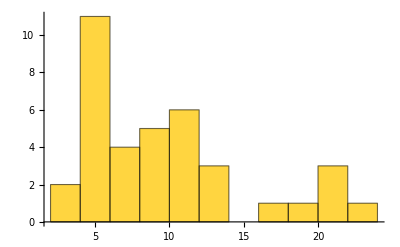

```mathematica
Histogram[Map[#[[2]]["peakYear"]&,bs[[obspos0//Flatten]]],{2}]
```

```mathematica
Map[#[[2]]["len"]&,bs[[obspos0//Flatten]]]//Commonest
```

{70,72}

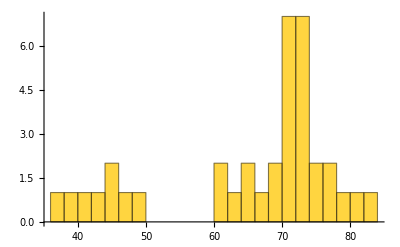

```mathematica
Histogram[Map[#[[2]]["len"]&,bs[[obspos0//Flatten]]],{2}]
```

相当に厳しい条件でのオブソレッセンス到達論文：

```mathematica
(obspos1=Position[Map[#[[-1]]&,Map[#[[2]]["acRatio"]&,bs]],x_/;x<0.002])//Length
```

59

```mathematica
Map[#[[2]]["peakYear"]&,bs[[obspos1//Flatten]]]//Commonest
```

{9}

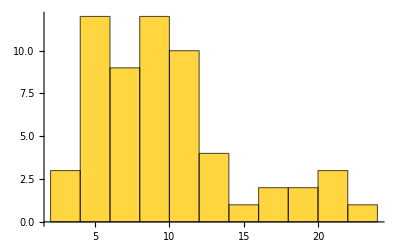

```mathematica
Histogram[Map[#[[2]]["peakYear"]&,bs[[obspos1//Flatten]]],{2},PlotRange->Full]
```

```mathematica
Map[#[[2]]["len"]&,bs[[obspos1//Flatten]]]//Commonest
```

{37}

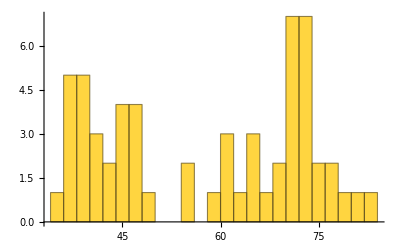

```mathematica
Histogram[Map[#[[2]]["len"]&,bs[[obspos1//Flatten]]],{2},PlotRange->Full]
```

ある程度厳しい条件でのオブソレッセンス到達論文：

```mathematica
(obspos2=Position[Map[#[[-1]]&,Map[#[[2]]["acRatio"]&,bs]],x_/;x<0.02])//Length
```

159

```mathematica
Map[#[[2]]["peakYear"]&,bs[[obspos2//Flatten]]]//Commonest
```

{10,5}

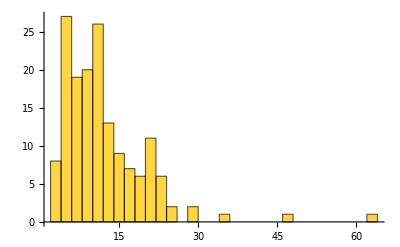

```mathematica
Histogram[Map[#[[2]]["peakYear"]&,bs[[obspos2//Flatten]]],{2},PlotRange->Full]
```

```mathematica
Map[#[[2]]["len"]&,bs[[obspos2//Flatten]]]//Commonest
```

{70,44}

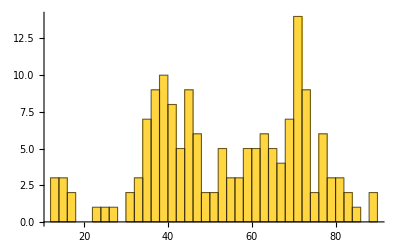

```mathematica
Histogram[Map[#[[2]]["len"]&,bs[[obspos2//Flatten]]],{2},PlotRange->Full]
```

オブソレッセンスベクトル （https://link.springer.com/article/10.1007/s11192-016-1884-7） を用いてみる。

#### オブソレッセンスSelection(3)

十分にオブソレッセンスがみられるものだけを抽出する。

・出版から十分な時間が経過している：”len”が十分に長い(10年以上)
・ピーク期が十分に過ぎ去っている：“decayPeriod”が“peakYear”以上
・被引用の傾向が十分に低下している：“decayPeriod”が”InDicay”でない（peakYear以降かつ当該年の引用数が当該年までの引用数の5%以下となる年のうち最も古い）

```mathematica
(obsolatedPos3=Flatten[Position[bs,x_/;x[[2]]["len"]>=10&&x[[2]]["decayPeriod"]>=x[[2]]["peakYear"]&&x[[2]]["decayPeriod"]!="InDecay"]])//Length
```

Part::partd: 部分指定List⟦2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: ∞の部分2は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

77

```mathematica
(nonobsolatedPos3=Complement[Table[n,{n,Length[bs]}],obsolatedPos3])//Length
```

459

多峰性を持つpos

```mathematica
obsmultiPos3=Intersection[allMultimodePos,obsolatedPos3]
```

{77,232,233,484,512}

```mathematica
obsolated3=top1PcCitedArtCitedCount["PY-2020"][[obsolatedPos3]];
```

```mathematica
obsolatedSort3["PY"]=SortBy[obsolated3,#[[1,1]]&];
```

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort3["PY"]],Joined->True,PlotRange->Full,AxesLabel->{"出版後の年数","出版後の年数による論文順位","被引用数"},ColorFunction->myColor2]
```

-Graphics3D-

チャンピオン論文がObsolateか確認する：

```mathematica
obsPMID=Association[Map[#[[1,2]]->#[[1,2]]&,bs[[obsolatedPos3]]]]
```

<|11130711→11130711,11181995→11181995,11373684→11373684,1175627→1175627,12466850→12466850,12989928→12989928,12991232→12991232,12996882→12996882,13069686→13069686,13124776→13124776,13186838→13186838,13319380→13319380,13610936→13610936,13767412→13767412,13944428→13944428,1400587→1400587,14287192→14287192,14381428→14381428,14454024→14454024,14474176→14474176,14530136→14530136,14822727→14822727,14862161→14862161,14907661→14907661,149110→149110,15260895→15260895,15297300→15297300,15398551→15398551,1555235→1555235,16255080→16255080,16595758→16595758,16694480→16694480,16748220→16748220,16748273→16748273,16748381→16748381,17237035→17237035,17247150→17247150,17488738→17488738,17554300→17554300,17751251→17751251,17760012→17760012,18016252→18016252,18156677→18156677,18287387→18287387,1852778→1852778,19171970→19171970,19325852→19325852,19474385→19474385,20610543→20610543,20981092→20981092,21546353→21546353,2199796→2199796,2448875→2448875,2449095→2449095,265521→265521,2659436→2659436,2999980→2999980,3162770→3162770,320200→320200,344137→344137,6091052→6091052,6159641→6159641,6232463→6232463,6246368→6246368,6260957→6260957,6266278→6266278,6269464→6269464,6286831→6286831,6295879→6295879,6295880→6295880,6310323→6310323,6329026→6329026,6791577→6791577,7494007→7494007,773363→773363,8242752→8242752,9278503→9278503|>

結果はいずれもObsolateでない：

```mathematica
Map[{pmidToTitle[#],#,obsPMID[#]}&, championPMID]
```

{{Qualitative analysis of proteins: a partition chromatographic method using paper.,16747784,Missing[KeyAbsent,16747784]},{Qualitative analysis of proteins: a partition chromatographic method using paper.,16747784,Missing[KeyAbsent,16747784]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Protein measurement with the Folin phenol reagent.,14907713,Missing[KeyAbsent,14907713]},{Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,5432063,Missing[KeyAbsent,5432063]},{Cleavage of structural proteins during the assembly of the head of bacteriophage T4.,5432063,Missing[KeyAbsent,5432063]}}

#### 最多被引用論文のオブソレッセンス状態Selection(3)

```mathematica
Union[championPMID]
```

{14907713,16747784,5432063}

順番を変える（出版順）

```mathematica
championPMIDunion={"16747784","14907713","5432063"}
```

{16747784,14907713,5432063}

位置

```mathematica
Position[bs,"16747784"]
Position[bs,"14907713"]
Position[bs,"5432063"]
```

{{200,1,2}}

{{134,1,2}}

{{440,1,2}}

```mathematica
championPMIDpos={200,134,440}
```

{200,134,440}

Gs関係指標：

```mathematica
championObsClass=Map[PMIDtoobsClass,championPMIDunion]
```

{FP,O,O}

```mathematica
championObsIdx={obsIdx[[200]][[-1]],
obsIdx[[134]][[-1]],
obsIdx[[440]][[-1]]}
```

{<|Gs→-0.663768,A-→-0.332126,A+→0.000241559,A→-0.331884,len→77|>,<|Gs→0.109566,A-→-0.0108832,A+→0.065666,A→0.0547828,len→70|>,<|Gs→0.075615,A-→-0.0146209,A+→0.0524285,A→0.0378075,len→51|>}

論文タイトル：

```mathematica
championPlotTitleunion={"Qualitative analysis of ...","Protein measurement with ...","Cleavage of structural proteins ..."}
```

{Qualitative analysis of ...,Protein measurement with ...,Cleavage of structural proteins ...}

```mathematica
championPlotTitleunionP={"Qualitative analysis of ... (1944)","Protein measurement with ... (1951)","Cleavage of structural proteins ... (1970)"}
```

{Qualitative analysis of ... (1944),Protein measurement with ... (1951),Cleavage of structural proteins ... (1970)}

表：

```mathematica
championoObsHead={"論文タイトル","クラス","A^-","A^+","Gs","年齢"}
```

{論文タイトル,クラス,A^-,A^+,Gs,年齢}

```mathematica
(championoObsTbl=Prepend[Prepend[Prepend[Transpose[Round[Map[{#["A-"],#["A+"],#["Gs"],#["len"]}&,championObsIdx],0.001]],championObsClass],championPlotTitleunion]//Transpose,championoObsHead])//TableForm
```

論文タイトル | クラス | A^- | A^+ | Gs | 年齢
Qualitative analysis of ... | FP | -0.332 | 0. | -0.664 | 77.
Protein measurement with ... | O | -0.011 | 0.066 | 0.11 | 70.
Cleavage of structural proteins ... | O | -0.015 | 0.052 | 0.076 | 51.

Plot：

```mathematica
plot3DPoints={obsAA[[obsFP]],obsAA[[obsSB]],obsAA[[obsNm]],obsAA[[obsOthers]]};
```

```mathematica
campion3Dpoints=Map[{#["A-"],#["A+"],#["Gs"]}&,championObsIdx]
```

{{-0.332126,0.000241559,-0.663768},{-0.0108832,0.065666,0.109566},{-0.0146209,0.0524285,0.075615}}

```mathematica
Position[plot3DPoints,campion3Dpoints[[1]]]
Position[plot3DPoints,campion3Dpoints[[2]]]
Position[plot3DPoints,campion3Dpoints[[3]]]
```

{{1,16}}

{{4,74}}

{{4,271}}

```mathematica
plot3DPoints[[1,16]]
plot3DPoints[[4,74]]
plot3DPoints[[4,271]]
```

{-0.332126,0.000241559,-0.663768}

{-0.0108832,0.065666,0.109566}

{-0.0146209,0.0524285,0.075615}

```mathematica
repInf={{1,16}->Callout[plot3DPoints[[1,16]],Text["Q"],Above],{4,74}->Callout[plot3DPoints[[4,74]],Text["P"],Above],{4,271}->Callout[plot3DPoints[[4,271]],Text["C"],Above]}
```

{{1,16}→Callout[{-0.332126,0.000241559,-0.663768},Q,Above],{4,74}→Callout[{-0.0108832,0.065666,0.109566},P,Above],{4,271}→Callout[{-0.0146209,0.0524285,0.075615},C,Above]}

```mathematica
ListPointPlot3D[ReplacePart[plot3DPoints,repInf],Filling->Bottom,AxesLabel->{"A-","A+","Gs"},PlotRange->All,PlotLegends->{"FP","SB","Nm","O"}]
```

-Graphics3D-

統計値：

```mathematica
pmidtobs=Association[Map[#[[1,2]]->#&,bs]];
```

```mathematica
topPMID=Map[pmidtobs,championPMIDunion]
```

{{{1944,16747784},<|len→77,peakYear→9,peakCount→23,peakRatio→0.129944,acRatio→{1.,0.8,0.375,0.5,0.542857,0.385965,0.278481,0.20202,0.188525,0.0895522,0.0945946,0.0691824,0.0809249,0.0225989,0.0274725,0.037037,0.0307692,0.0151515,0.01,0.0291262,0.0190476,0.00943396,0.00469484,0.0138889,0.00460829,0.00458716,0.0135747,0.,0.,0.,0.0045045,0.,0.,0.0044843,0.00446429,0.,0.,0.,0.,0.,0.,0.00444444,0.,0.,0.,0.00442478,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00440529,0.00438596,0.,0.,0.,0.,0.00436681,0.00434783,0.004329,0.,0.,0.,0.,0.00431034,0.00429185,0.0042735,0.00425532,0.00423729,0.},peakPosition→0.642857,sustainYear→68,decayCited→177,decayPeriod→5,firstCitedYear→0,totalCited→236,V:Av5year→28.3951,V:diff→1.20154,V:diff2→0.604079,diffTotal→-7.,diffSeq→{21/5,18/5,17/5,3,-7/5,-8/5,-11/5,-6/5,-19/5,-7/5,-7/5,-1,-11/5,-2/5,1/5,-3/5,-4/5,-2/5,1/5,-1,-3/5,1/5,-1/5,-3/5,-1/5,0,-3/5,0,1/5,1/5,-1/5,0,0,-1/5,-1/5,0,1/5,0,0,0,1/5,-1/5,0,0,0,-1/5,0,0,0,0,0,0,0,1/5,1/5,0,0,0,-1/5,0,1/5,1/5,0,0,-1/5,-1/5,0,1/5,1/5,1/5,1/5,-1/5,-1/5,-1/5,-1/5,-1/5}|>},{{1951,14907713},<|len→70,peakYear→28,peakCount→1740,peakRatio→0.0585012,acRatio→{1,1.,0.833333,0.684211,0.55814,0.358209,0.355769,0.292517,0.293269,0.306667,0.259259,0.25,0.223022,0.232892,0.238655,0.221714,0.227778,0.218318,0.193055,0.190144,0.190645,0.180106,0.1621,0.156053,0.142442,0.13684,0.128135,0.119678,0.103637,0.086866,0.0778216,0.0762517,0.0673167,0.0665915,0.0588975,0.0539365,0.0507075,0.0472044,0.0437872,0.0391091,0.0344797,0.0316553,0.0288896,0.0265658,0.0252821,0.0187753,0.0140827,0.0123576,0.0118593,0.0106639,0.00842967,0.00852884,0.00999202,0.00801594,0.0103085,0.0110868,0.0102985,0.0134624,0.0135961,0.0151502,0.017318,0.017425,0.0185998,0.0192156,0.0176959,0.0158343,0.0151993,0.0148378,0.0148848,0.0147408},peakPosition→0.736842,sustainYear→42,decayCited→29743,decayPeriod→10,firstCitedYear→1,totalCited→53050,V:Av5year→256971.,V:diff→5510.1,V:diff2→605.608,diffTotal→147.8,diffSeq→{24/5,36/5,38/5,48/5,68/5,81/5,98/5,112/5,30,192/5,234/5,316/5,398/5,79,453/5,574/5,601/5,577/5,683/5,127,614/5,588/5,122,392/5,171/5,-28/5,-10,-47,-86/5,-44/5,-48/5,-153/5,-101/5,-233/5,-233/5,-59,-341/5,-374/5,-389/5,-316/5,-437/5,-549/5,-544/5,-501/5,-521/5,-377/5,-198/5,-73/5,-138/5,1,26,94/5,174/5,267/5,246/5,319/5,367/5,294/5,327/5,38,0,-39/5,-117/5,-30,-88/5,-791/5,-771/5,-764/5,-778/5}|>},{{1970,5432063},<|len→51,peakYear→23,peakCount→2261,peakRatio→0.0701194,acRatio→{1.,0.875,0.714286,0.658537,0.484277,0.423913,0.35514,0.413699,0.33576,0.32865,0.296217,0.262758,0.235337,0.220627,0.213373,0.195072,0.177229,0.159332,0.141538,0.132943,0.118302,0.108816,0.0986087,0.0839759,0.0723075,0.0692653,0.0565608,0.0470461,0.0402988,0.0345392,0.0279593,0.0269345,0.0237735,0.0227656,0.0211918,0.0202651,0.0181157,0.0201196,0.0226794,0.0210126,0.0212385,0.0226621,0.0231847,0.0234554,0.0222794,0.0198555,0.0182744,0.016884,0.0155376,0.0157791,0.0151892},peakPosition→0.821429,sustainYear→28,decayCited→32245,decayPeriod→5,firstCitedYear→0,totalCited→54249,V:Av5year→380198.,V:diff→12712.1,V:diff2→1212.23,diffTotal→133.,diffSeq→{116/5,29,282/5,63,461/5,572/5,677/5,669/5,799/5,898/5,942/5,972/5,191,165,723/5,548/5,448/5,67,109/5,-208/5,-171/5,-511/5,-744/5,-748/5,-749/5,-1007/5,-747/5,-621/5,-476/5,-367/5,-186/5,-249/5,-11,92/5,83/5,133/5,293/5,243/5,153/5,173/5,44/5,-21,-42,-306/5,-248/5,-168/5,-186,-874/5,-817/5,-843/5}|>}}

```mathematica
jobsItemName={"論文タイトル","最大被引用を得るまでの期間","減衰期間","最大被引用数（年間）","減衰年の被引用数","被引用数分散","被引用速度の分散","被引用か速度の分散"}
```

{論文タイトル,最大被引用を得るまでの期間,減衰期間,最大被引用数（年間）,減衰年の被引用数,被引用数分散,被引用速度の分散,被引用か速度の分散}

```mathematica
obsItemName={"Title","Peak period\n(year)","Decay period\n(year)","Peak count","Decay cited","Variance:cited","Variance:diff","Variance:diff-accel"}
```

{Title,Peak period
(year),Decay period
(year),Peak count,Decay cited,Variance:cited,Variance:diff,Variance:diff-accel}

```mathematica
obsValue=Map[{#[[2]]["peakYear"],#[[2]]["decayPeriod"],#[[2]]["peakCount"],#[[2]]["decayCited"],Round[#[[2]]["V:Av5year"],0.1],Round[#[[2]]["V:diff"],0.1],Round[#[[2]]["V:diff2"],0.1]}&,topPMID]
```

{{9,5,23,177,28.4,1.2,0.6},{28,10,1740,29743,256971.,5510.1,605.6},{23,5,2261,32245,380198.,12712.1,1212.2}}

```mathematica
obsValueT=Map[Flatten,{championPlotTitleunion,obsValue}//Transpose]
```

{{Qualitative analysis of ...,9,5,23,177,28.4,1.2,0.6},{Protein measurement with ...,28,10,1740,29743,256971.,5510.1,605.6},{Cleavage of structural proteins ...,23,5,2261,32245,380198.,12712.1,1212.2}}

オブソレッセンスに関する諸元表：

```mathematica
Prepend[obsValueT,obsItemName]//TableForm
```

Title | Peak period
(year) | Decay period
(year) | Peak count | Decay cited | Variance:cited | Variance:diff | Variance:diff-accel
Qualitative analysis of ... | 9 | 5 | 23 | 177 | 28.4 | 1.2 | 0.6
Protein measurement with ... | 28 | 10 | 1740 | 29743 | 256971. | 5510.1 | 605.6
Cleavage of structural proteins ... | 23 | 5 | 2261 | 32245 | 380198. | 12712.1 | 1212.2

```mathematica
TABmcpapers=Prepend[obsValueT,jobsItemName]//TableForm
```

論文タイトル | 最大被引用を得るまでの期間 | 減衰期間 | 最大被引用数（年間） | 減衰年の被引用数 | 被引用数分散 | 被引用速度の分散 | 被引用か速度の分散
Qualitative analysis of ... | 9 | 5 | 23 | 177 | 28.4 | 1.2 | 0.6
Protein measurement with ... | 28 | 10 | 1740 | 29743 | 256971. | 5510.1 | 605.6
Cleavage of structural proteins ... | 23 | 5 | 2261 | 32245 | 380198. | 12712.1 | 1212.2

```mathematica
(*Export[exportdocdir<>"TABmcpapers.tex",TABmcpapers,"TeXFragment"]*)
```

```mathematica
championArtPointlist=DeleteCases[(Map[(#[[2]]//Normal)/.{Rule->List}&,top1PcCitedArtCitedyearAssociations[[{200,134,440}]]]//ToExpression),{2024,_},-1]
```

{{{1944,1},{1945,4},{1946,3},{1947,8},{1948,19},{1949,22},{1950,22},{1951,20},{1952,23},{1953,12},{1954,14},{1955,11},{1956,14},{1957,4},{1958,5},{1959,7},{1960,6},{1961,3},{1962,2},{1963,6},{1964,4},{1965,2},{1966,1},{1967,3},{1968,1},{1969,1},{1970,3},{1974,1},{1977,1},{1978,1},{1985,1},{1989,1},{2002,1},{2003,1},{2008,1},{2009,1},{2010,1},{2015,1},{2016,1},{2017,1},{2018,1},{2019,1},{2021,2},{2022,2},{2023,2}},{{1952,1},{1953,5},{1954,13},{1955,24},{1956,24},{1957,37},{1958,43},{1959,61},{1960,92},{1961,105},{1962,135},{1963,155},{1964,211},{1965,284},{1966,339},{1967,451},{1968,553},{1969,606},{1970,737},{1971,913},{1972,1052},{1973,1130},{1974,1289},{1975,1372},{1976,1527},{1977,1640},{1978,1740},{1979,1681},{1980,1543},{1981,1499},{1982,1590},{1983,1505},{1984,1595},{1985,1499},{1986,1451},{1987,1437},{1988,1404},{1989,1362},{1990,1266},{1991,1156},{1992,1096},{1993,1030},{1994,973},{1995,950},{1996,719},{1997,547},{1998,486},{1999,472},{2000,429},{2001,342},{2002,349},{2003,413},{2004,334},{2005,434},{2006,472},{2007,443},{2008,587},{2009,601},{2010,680},{2011,791},{2012,810},{2013,881},{2014,928},{2015,870},{2016,791},{2017,771},{2018,764},{2019,778},{2020,782},{2021,792},{2022,805},{2023,771}},{{1970,1},{1971,7},{1972,20},{1973,54},{1974,77},{1975,117},{1976,152},{1977,302},{1978,369},{1979,538},{1980,689},{1981,829},{1982,971},{1983,1168},{1984,1436},{1985,1631},{1986,1801},{1987,1926},{1988,1993},{1989,2159},{1990,2179},{1991,2249},{1992,2261},{1993,2102},{1994,1951},{1995,2008},{1996,1738},{1997,1517},{1998,1354},{1999,1202},{2000,1001},{2001,991},{2002,896},{2003,878},{2004,835},{2005,815},{2006,742},{2007,841},{2008,970},{2009,918},{2010,948},{2011,1035},{2012,1084},{2013,1123},{2014,1091},{2015,992},{2016,930},{2017,874},{2018,817},{2019,843},{2020,824},{2021,863},{2022,804},{2023,665}}}

被引用推移のplot図：

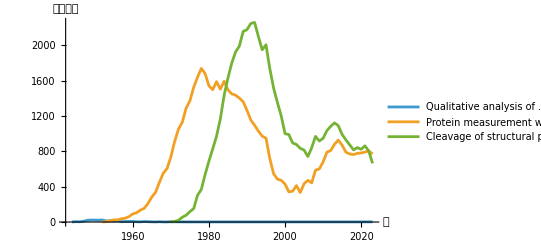

```mathematica
ListLinePlot[championArtPointlist,PlotLegends->championPlotTitleunionP,AxesLabel->{"年","被引用数"}]
```

```mathematica
ListLinePlot[championArtPointlist,PlotLabels->championPlotTitleunionP,AxesLabel->{"年","被引用数"}]
```

-Graphics-

```mathematica
championPlotTitleunionAT= Placed[championPlotTitleunionP,Above]
```

Placed[{Qualitative analysis of ... (1944),Protein measurement with ... (1951),Cleavage of structural proteins ... (1970)},Above]

```mathematica
ListLinePlot[championArtPointlist,PlotLabels->championPlotTitleunionAT,AxesLabel->{"年","被引用数"},PlotRange->{{1940,2025},All}]
```

-Graphics-

#### 指標plot(all)

```mathematica
bs//Length
```

536

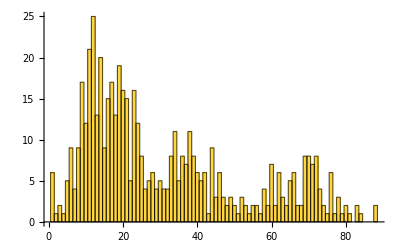

```mathematica
Histogram[Map[#[[2]]["len"]&,bs],{1},PlotRange->Full]
```

```mathematica
Map[#[[2]]["len"]&,bs]//Max
Map[#[[2]]["len"]&,bs]//Min
```

88

1

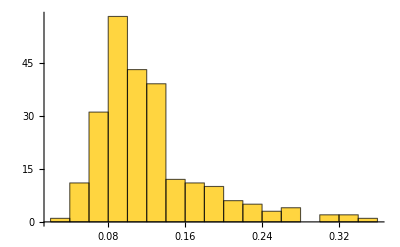

```mathematica
Histogram[Map[#[[2]]["peakRatio"]&,bs],PlotRange->Full]
```

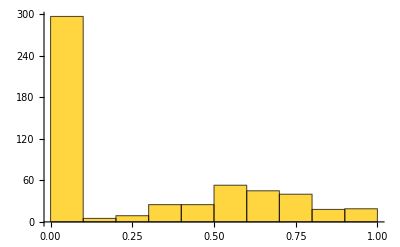

```mathematica
Histogram[Map[#[[2]]["peakPosition"]&,bs],PlotRange->Full]
```

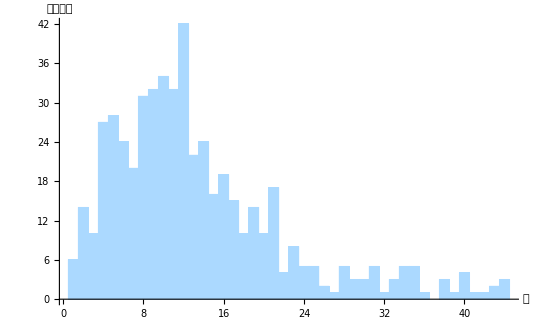

```mathematica
hi["peakYear","all"]=Labeled[Histogram[Map[#[[2]]["peakYear"]&,bs],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},ImageSize->imsz4],"1 出版からピークまで"]
```

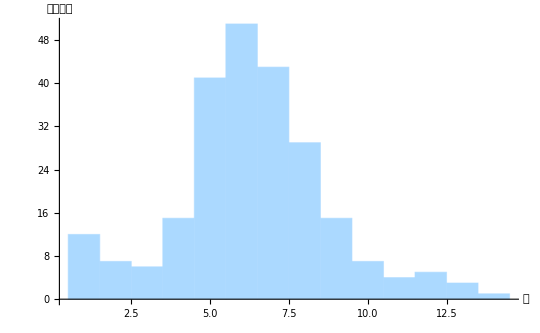

```mathematica
hi["decayPeriod","all"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]&,bs],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},ImageSize->imsz4],"2 ピークから減衰まで"]
```

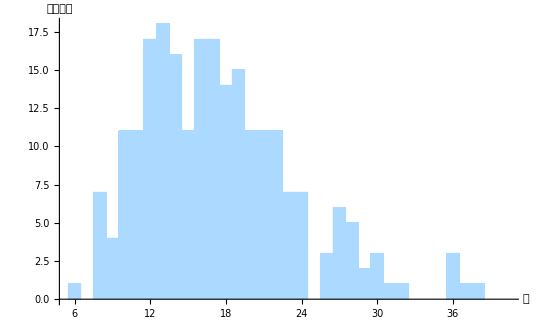

```mathematica
hi["activePeriod","all"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]+#[[2]]["peakYear"]&,bs],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},ImageSize->imsz4],"3 出版から減衰まで"]
```

"InDecay" のカウント

```mathematica
Cases[Map[#[[2]]["decayPeriod"]&,bs],_String]//Length
```

297

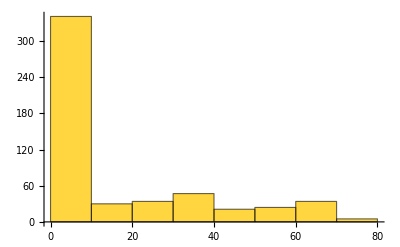

```mathematica
Histogram[Map[#[[2]]["sustainYear"]&,bs]]
```

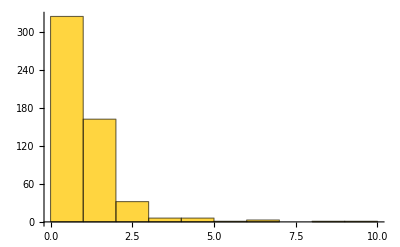

```mathematica
Histogram[Map[#[[2]]["firstCitedYear"]&,bs]]
```

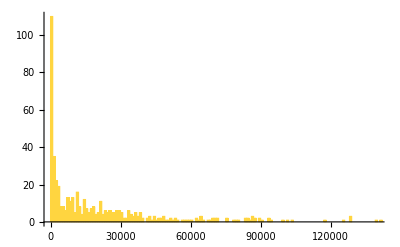

```mathematica
Histogram[Map[#[[2]]["V:Av5year"]&,bs],{1000}]
```

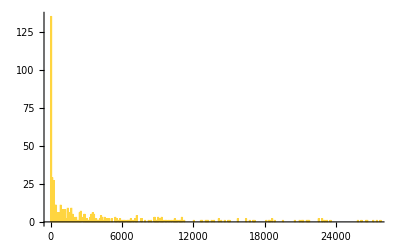

```mathematica
Histogram[Map[#[[2]]["V:diff"]&,bs],{100}]
```

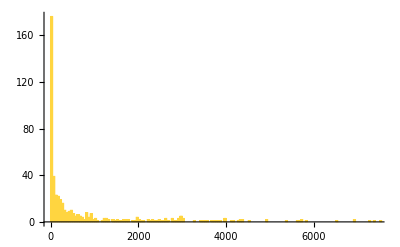

```mathematica
Histogram[Map[#[[2]]["V:diff2"]&,bs],{50}]
```

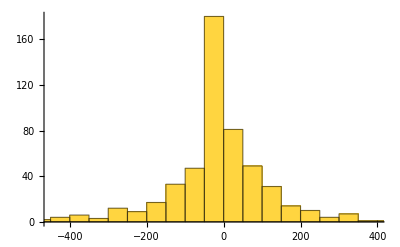

```mathematica
Histogram[Map[#[[2]]["diffTotal"]&,bs]]
```

#### 指標plot(obs/selection 3)

```mathematica
bs//Length
```

536

```mathematica
(obsbs3=bs[[obsolatedPos3]])//Length
```

77

```mathematica
Keys[obsbs3[[1,2]]]
```

{len,peakYear,peakCount,peakRatio,acRatio,peakPosition,sustainYear,decayCited,decayPeriod,firstCitedYear,totalCited,V:Av5year,V:diff,V:diff2,diffTotal,diffSeq}

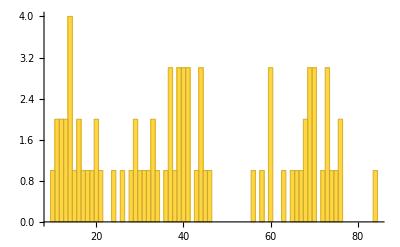

```mathematica
Histogram[Map[#[[2]]["len"]&,obsbs3],{1}]
```

```mathematica
Map[#[[2]]["len"]&,obsbs3]//Max
Map[#[[2]]["len"]&,obsbs3]//Min
```

84

10

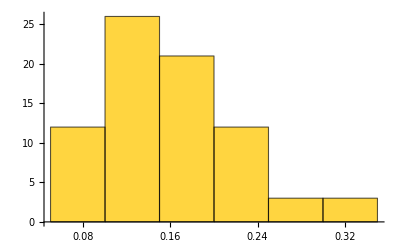

```mathematica
Histogram[Map[#[[2]]["peakRatio"]&,obsbs3],PlotRange->Full]
```

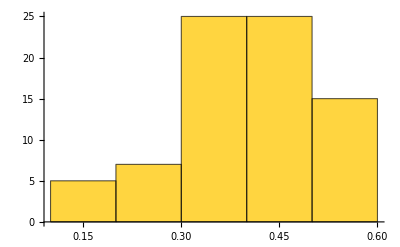

```mathematica
Histogram[Map[#[[2]]["peakPosition"]&,obsbs3],PlotRange->Full]
```

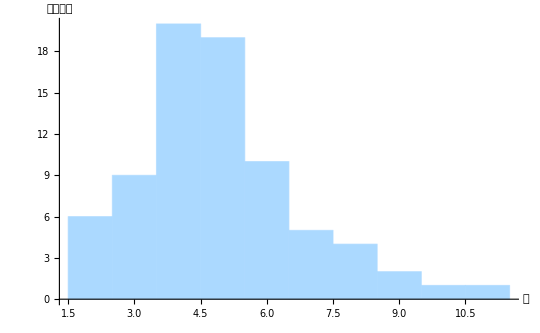

```mathematica
hi["peakYear","obs"]=Labeled[Histogram[Map[#[[2]]["peakYear"]&,obsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->imsz4],"1 出版からピークまで（n=77）"]
```

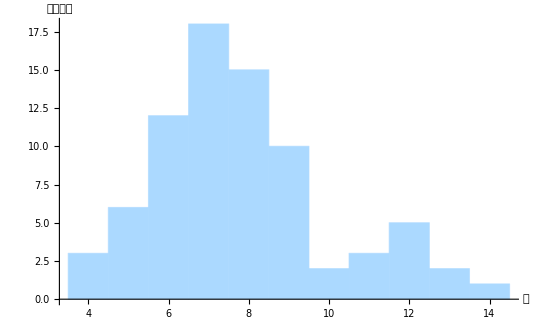

```mathematica
hi["decayPeriod","obs"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]&,obsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->imsz4],"2 ピークから減衰まで（n=77）"]
```

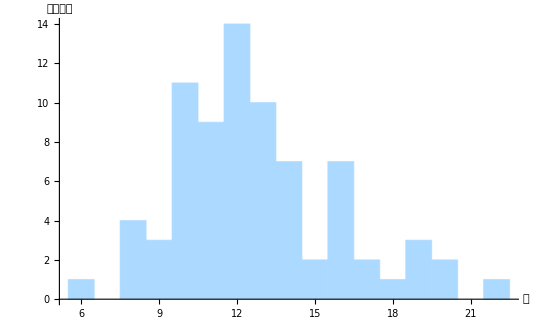

```mathematica
hi["activePeriod","obs"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]+#[[2]]["peakYear"]&,obsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->imsz4],"3 出版から減衰まで（n=77）"]
```

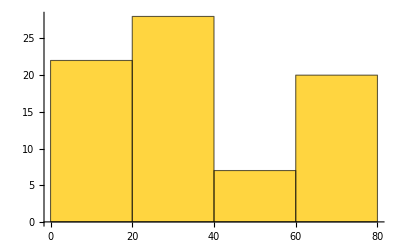

```mathematica
Histogram[Map[#[[2]]["sustainYear"]&,obsbs3]]
```

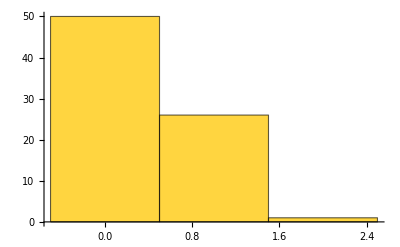

```mathematica
Histogram[Map[#[[2]]["firstCitedYear"]&,obsbs3]]
```

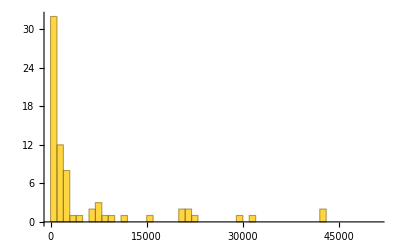

```mathematica
Histogram[Map[#[[2]]["V:Av5year"]&,obsbs3],{1000}]
```

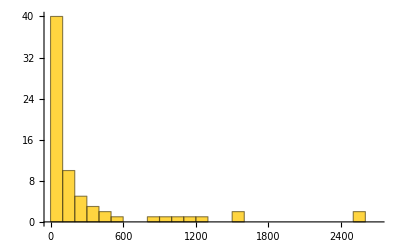

```mathematica
Histogram[Map[#[[2]]["V:diff"]&,obsbs3],{100}]
```

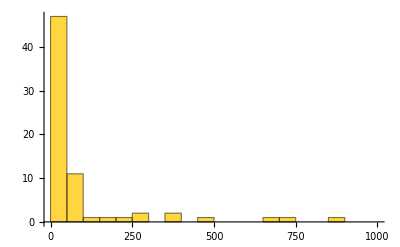

```mathematica
Histogram[Map[#[[2]]["V:diff2"]&,obsbs3],{50}]
```

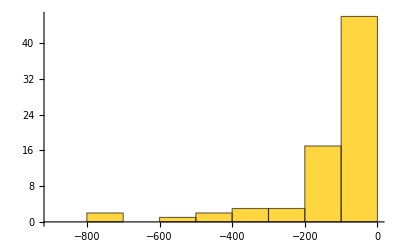

```mathematica
Histogram[Map[#[[2]]["diffTotal"]&,obsbs3]]
```

#### 指標plot(nonobs/selection 3)

```mathematica
bs//Length
```

536

```mathematica
(nonobsbs3=bs[[nonobsolatedPos3]])//Length
```

459

```mathematica
Keys[nonobsbs3[[1,2]]]
```

{len,peakYear,peakCount,peakRatio,acRatio,peakPosition,sustainYear,decayCited,decayPeriod,firstCitedYear,totalCited,V:Av5year,V:diff,V:diff2,diffTotal,diffSeq}

```mathematica
Map[#[[2]]["len"]&,nonobsbs3]//Length
```

459

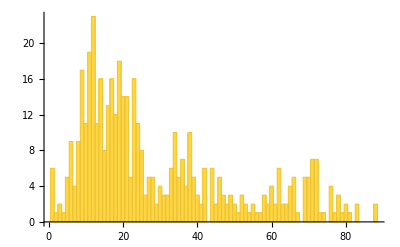

```mathematica
Histogram[Map[#[[2]]["len"]&,nonobsbs3],{1}]
```

```mathematica
Map[#[[2]]["len"]&,nonobsbs3]//Max
Map[#[[2]]["len"]&,nonobsbs3]//Min
```

88

1

```mathematica
Cases[Map[#[[2]]["peakYear"]&,nonobsbs3],_Integer]//Length
```

459

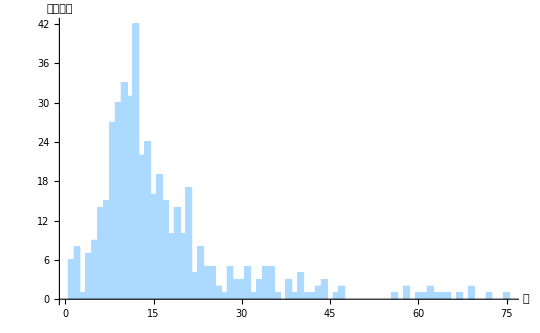

```mathematica
hi["peakYear","nonobs"]=Labeled[Histogram[Map[#[[2]]["peakYear"]&,nonobsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->imsz4],"1 出版からピークまで（n=459）"]
```

```mathematica
Cases[Map[#[[2]]["decayPeriod"]&,nonobsbs3],_Integer]//Length
```

162

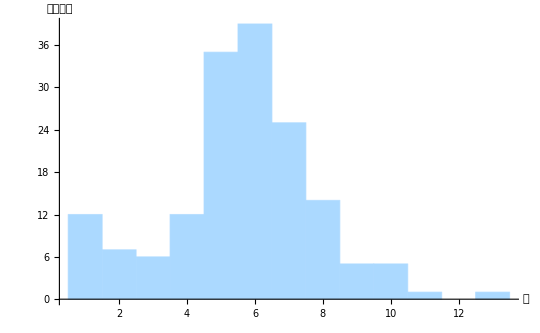

```mathematica
hi["decayPeriod","nonobs"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]&,nonobsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->imsz4],"2 ピークから減衰まで（n=162）"]
```

```mathematica
Cases[Map[#[[2]]["decayPeriod"]+#[[2]]["peakYear"]&,nonobsbs3],_Integer]//Length
```

162

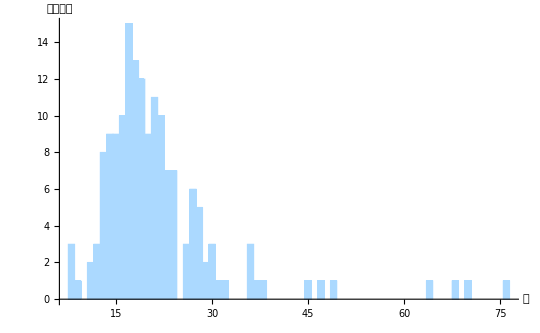

```mathematica
hi["activePeriod","nonobs"]=Labeled[Histogram[Map[#[[2]]["decayPeriod"]+#[[2]]["peakYear"]&,nonobsbs3],{1},ChartStyle->RGBColor[0.669, 0.852, 1],AxesLabel->{"年","被引用数"},PlotRange->Full,ImageSize->imsz4],"3 出版から減衰まで（n=162）"]
```

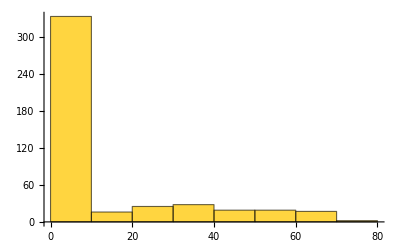

```mathematica
Histogram[Map[#[[2]]["sustainYear"]&,nonobsbs3]]
```

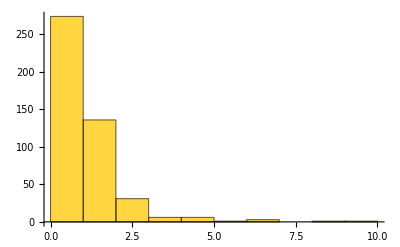

```mathematica
Histogram[Map[#[[2]]["firstCitedYear"]&,nonobsbs3]]
```

#### 指標plot tbl (all + selection 3)

```mathematica
tbl["index plot"]={{"高被引用論文全体",hi["peakYear","all"],hi["decayPeriod","all"],hi["activePeriod","all"]},
{"オブソレッセンス状態\nにある論文のみ",hi["peakYear","obs"],hi["decayPeriod","obs"],hi["activePeriod","obs"]}
}//TableForm
```

高被引用論文全体 | -Graphics- | -Graphics- | -Graphics-
オブソレッセンス状態
にある論文のみ | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*Export[exportdocdir<>"obsindex1-1.eps",hi["peakYear","all"]]
Export[exportdocdir<>"obsindex1-2.eps",hi["decayPeriod","all"]]
Export[exportdocdir<>"obsindex1-3.eps",hi["activePeriod","all"]]
Export[exportdocdir<>"obsindex2-1.eps",hi["peakYear","obs"]]
Export[exportdocdir<>"obsindex2-2.eps",hi["decayPeriod","obs"]]
Export[exportdocdir<>"obsindex2-3.eps",hi["activePeriod","obs"]]*)
```

#### 指標plot tbl ((obs + nonobs)/selection 3)

```mathematica
tbl["index plot"]={{"オブソレッセンス\n状態にない論文",hi["peakYear","nonobs"],hi["decayPeriod","nonobs"],hi["activePeriod","nonobs"]},
{"オブソレッセンス\n状態にある論文",hi["peakYear","obs"],hi["decayPeriod","obs"],hi["activePeriod","obs"]}
}//TableForm
```

オブソレッセンス
状態にない論文 | -Graphics- | -Graphics- | -Graphics-
オブソレッセンス
状態にある論文 | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*exportdocdir="/Volumes/LaCie/BANK/pubmed-analysis/202312/"
Export[exportdocdir<>"obsindex1-1.eps",hi["peakYear","nonobs"]]
Export[exportdocdir<>"obsindex1-2.eps",hi["decayPeriod","nonobs"]]
Export[exportdocdir<>"obsindex1-3.eps",hi["activePeriod","nonobs"]]
Export[exportdocdir<>"obsindex2-1.eps",hi["peakYear","obs"]]
Export[exportdocdir<>"obsindex2-2.eps",hi["decayPeriod","obs"]]
Export[exportdocdir<>"obsindex2-3.eps",hi["activePeriod","obs"]]*)
```

#### クラスタリングに用いる指標の選択

```mathematica
(*{Table[n,{n,Length[obsbs2[[1,2]]]}],obsbs2[[1,2]]//Keys}//TableForm*)
```

2. peakYear
8. decayPeriod
3. peakCount
7. decayCited
11. V:Av5year
12. V:diff
13. Vdiff2

```mathematica
{Table[n,{n,Length[obsbs3[[1,2]]]}],obsbs3[[1,2]]//Keys}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
len | peakYear | peakCount | peakRatio | acRatio | peakPosition | sustainYear | decayCited | decayPeriod | firstCitedYear | totalCited | V:Av5year | V:diff | V:diff2 | diffTotal | diffSeq

```mathematica
vselP={2,8,3,7,11,12,13}
```

{2,8,3,7,11,12,13}

```mathematica
vselPlen=Length[vselP]
```

7

#### クラスタリング（selection 3 / 7 indices）

サンプル名・サンプルPos

```mathematica
(bsObs3=bs[[obsolatedPos3]])//Length
```

77

```mathematica
posMap3=Table[n->obsolatedPos3[[n]],{n,Length[obsolatedPos3]}]
```

{1→20,2→22,3→31,4→39,5→59,6→72,7→73,8→75,9→76,10→77,11→79,12→88,13→93,14→104,15→107,16→110,17→113,18→114,19→118,20→119,21→120,22→128,23→130,24→133,25→135,26→148,27→151,28→159,29→166,30→182,31→185,32→188,33→203,34→204,35→205,36→216,37→218,38→222,39→224,40→232,41→233,42→238,43→242,44→244,45→248,46→263,47→267,48→274,49→302,50→306,51→313,52→320,53→354,54→355,55→369,56→370,57→386,58→390,59→394,60→405,61→446,62→447,63→450,64→452,65→454,66→455,67→456,68→458,69→459,70→460,71→461,72→465,73→474,74→483,75→484,76→490,77→512}

```mathematica
(sampleObs3PMID=Map[#[[1,2]]&,bsObs3])//Length
```

77

```mathematica
(sampleObs3Pos=Table[n,{n,Length[bsObs3]}])//Length
```

77

データチューニング

```mathematica
(nmObs3Pre=toItemNormarizeMat[bsObs3])//Dimensions
```

Normalize::nlnmt2: 第1引数が数でもベクトルでもないか，第2引数がどのような数値的引数に対しても常に非負の実数を返すノルム関数でないかのいずれかです．

General::stop: この計算中に，Normalize::nlnmt2のこれ以上の出力は表示されません．

Transpose::nmtx: {«1»}の最初の2個のレベルは転置できません．

{1}

plotデータ

```mathematica
(nmObs3=Map[#[[vselP]]&,nmObs3Pre])//Dimensions
```

{77,7}

```mathematica
(nmZObs3=Prepend[nmObs3,Table[0,{vselPlen}]])//Dimensions
```

{78,7}

```mathematica
(nmtObs3=Map[totalize,nmObs3])//Dimensions
```

{77,7}

```mathematica
(nmtZObs3=Prepend[nmtObs3,Table[0,{vselPlen}]])//Dimensions
```

{78,7}

PCA

```mathematica
nmObs3PCA=PrincipalComponents[nmObs3];
```

```mathematica
nmZObs3PCA=PrincipalComponents[nmZObs3];
```

```mathematica
nmtObs3PCA=PrincipalComponents[nmtObs3];
```

```mathematica
nmtZObs3PCA=PrincipalComponents[nmtZObs3];
```

plot

```mathematica
Graphics3D[Map[Point[#[[;;3]]]&,nmObs3PCA]]
```

-Graphics3D-

```mathematica
Graphics3D[{Map[Point[#[[;;3]]]&,nmZObs3PCA[[2;;]]],Red,Point[nmZObs3PCA[[1]][[;;3]]]}]
```

-Graphics3D-

```mathematica
Graphics3D[Map[Point[#[[;;3]]]&,nmtObs3PCA]]
```

-Graphics3D-

```mathematica
Graphics3D[{Map[Point[#[[;;3]]]&,nmtZObs3PCA[[2;;]]],Red,Point[nmtZObs3PCA[[1]][[;;3]]]}]
```

-Graphics3D-

クラスタリング
nmObs3に対してユークリッド距離を使うのが良いか。

```mathematica
clusteredPosObs3["SD","Agg"]=FindClusters[nmObs3->sampleObs3Pos,DistanceFunction->CosineDistance,CriterionFunction->"StandardDeviation",Method->"Agglomerate"]
```

{{26,50},{39},{27},{54,74,77},{16,29,45,52,55,57,58,60,61,62,66,69,71,72,76},{4,14,17,25,59,65,68,73},{67,70},{63},{21,30,31,47},{1,56},{3,5},{53,64},{2},{6,7,8,9,10,11,12,13,15,18,19,20,22,23,24,28,32,33,34,35,37,40,41,42},{44,46,48,49},{36},{75},{38},{51},{43}}

```mathematica
clusteredPosObs3["Dunn","Agg"]=FindClusters[nmObs3->sampleObs3Pos,DistanceFunction->CosineDistance,CriterionFunction->"Dunn",Method->"Agglomerate"]
```

{{26,50},{39},{27},{54,74,77},{16,29,45,52,55,57,58,60,61,62,66,69,71,72,76},{4,14,17,25,59,65,68,73},{67,70},{63},{21,30,31,47},{1,56},{3,5},{53,64},{2},{6,7,8,9,10,11,12,13,15,18,19,20,22,23,24,28,32,33,34,35,37,40,41,42},{44,46,48,49},{36},{75},{38},{51},{43}}

```mathematica
clusteredPosObs3["Dunn","Agg","Ecld"]=FindClusters[nmObs3->sampleObs3Pos,DistanceFunction->EuclideanDistance,CriterionFunction->"Dunn",Method->"Agglomerate"]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77}}

```mathematica
clusteredPosObs3["Dunn","Agg","Ecld"]//Length
```

1

```mathematica
classMembers=Map[Length,clusteredPosObs3["Dunn","Agg","Ecld"]]
```

{77}

```mathematica
dendroID=Map[Rotate[#,-Pi/2,{1,1}]
&,sampleObs3Pos]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77}

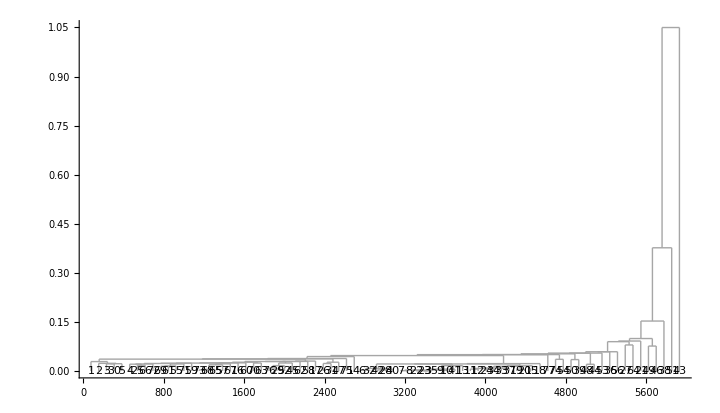

```mathematica
dendroplot=Dendrogram[nmObs3->dendroID,DistanceFunction->EuclideanDistance, Axes->{False, True},ImageSize->720,AspectRatio->1/1.74]
```

```mathematica
nmObs3group["Mn"]={43,51,38,49,46}
```

{43,51,38,49,46}

IDのテキスト表示

```mathematica
txcood=Map[#[[;;3]]&,nmObs3PCA][[nmObs3group["Mn"]]]-0.02
```

{{-1.70334,-0.21118,0.0379886},{-0.719389,0.0161381,-0.0859375},{-0.3573,0.0554033,-0.052252},{-0.199776,0.0753523,-0.0965804},{-0.260122,0.0854121,-0.0684681}}

```mathematica
tx3d=Table[Text[nmObs3group["Mn"][[n]],txcood[[n]]],{n,Length[txcood]}]
```

{Text[43,{-1.70334,-0.21118,0.0379886}],Text[51,{-0.719389,0.0161381,-0.0859375}],Text[38,{-0.3573,0.0554033,-0.052252}],Text[49,{-0.199776,0.0753523,-0.0965804}],Text[46,{-0.260122,0.0854121,-0.0684681}]}

```mathematica
(nmObs3group["Mj"]=Complement[Table[n,{n,77}],nmObs3group["Mn"]])//Length
```

72

```mathematica
pcaplot=Graphics3D[{PointSize->0.02,Red,Map[Point[#[[;;3]]]&,nmObs3PCA][[nmObs3group["Mn"]]],Green,Map[Point[#[[;;3]]]&,nmObs3PCA][[nmObs3group["Mj"]]],Black,tx3d},ImageSize->500,ViewPoint->{0, 1.8, -(Pi+0.06)}]
```

-Graphics3D-

デントログラムとPCAの重ね書き

```mathematica
Show[dendroplot,Graphics[Inset[pcaplot]]]
```

-Graphics-

```mathematica
Show[dendroplot,Graphics[Inset[Rotate[pcaplot,0.12Pi]]]]
```

-Graphics-

多峰性を持つ論文がどのクラスに属するか

```mathematica
obsmultiPos3
```

{77,232,233,484,512}

```mathematica
clusteredPosObs3["Dunn","Agg","Ecld"]/.posMap3
```

{{20,22,31,39,59,72,73,75,76,77,79,88,93,104,107,110,113,114,118,119,120,128,130,133,135,148,151,159,166,182,185,188,203,204,205,216,218,222,224,232,233,238,242,244,248,263,267,274,302,306,313,320,354,355,369,370,386,390,394,405,446,447,450,452,454,455,456,458,459,460,461,465,474,483,484,490,512}}

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort3["PY"][[clusteredPosObs3["Dunn","Agg","Ecld"][[1]]]]],PlotRange->Full,AxesLabel->{"Elapsed year from publish","ID (sort by publish year)","Cited count"},ColorFunction->myColor2]
```

-Graphics3D-

```mathematica
ListLinePlot3D[Map[#[[2]]&,obsolatedSort3["PY"][[clusteredPosObs3["Dunn","Agg","Ecld"][[2]]]]],PlotRange->Full,AxesLabel->{"Elapsed year from publish","ID (sort by publish year)","Cited count"},ColorFunction->myColor2]
```

Part::partw: {{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,«27»}}の部分2は存在しません．

Part::pkspec1: 式{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,«27»}}⟦2⟧は部分指定に使用できません．

ListLinePlot3D::ldata: {0,4,6,5,8,4,3,4,4,4,1,2,0,1,1,0,1,1,3,0,1,2,3,0,0,0,2,0,0,1,2,1,1,1,0,1,1,0,0,1,1,0,0,0,2,0,0,0,1,0,«26»}は有効なデータ集合でもデータ集合のリストでもありません．

ListLinePlot3D[{0,4,6,5,8,4,3,4,4,4,1,2,0,1,1,0,1,1,3,0,1,2,3,0,0,0,2,0,0,1,2,1,1,1,0,1,1,0,0,1,1,0,0,0,2,0,0,0,1,0,1,0,0,0,0,2,1,0,1,2,1,1,0,0,1,0,0,2,1,3,1,1,1,2,2,4},PlotRange→Full,AxesLabel→{Elapsed year from publish,ID (sort by publish year),Cited count},ColorFunction→myColor2]

```mathematica
bs//Length
```

536

```mathematica
bsObs3//Length
```

77

#### 順位相関

ケンドールの順位相関（与える値は順位ではなく元の値）

```mathematica
kendalllist=Table[KendallTau[Transpose[Map[#[[2]]&,top1PcCitedArtCitedCount["1933-2020"]]][[n-1]],Transpose[Map[#[[2]]&,top1PcCitedArtCitedCount["1933-2020"]]][[n]]]//N,{n,2,88}]
```

KendallTau::zrvr: 入力されたデータはゼロ分散です．統計値は計算できません．

{Indeterminate,1.,0.998129,0.49579,0.63216,0.999062,0.997935,0.909069,0.728078,0.631029,0.710815,0.791508,0.755246,0.863018,0.824873,0.869172,0.873767,0.881803,0.865943,0.919497,0.928155,0.930918,0.907636,0.887656,0.916051,0.942813,0.920546,0.926952,0.913534,0.896434,0.900128,0.913615,0.909911,0.922554,0.941483,0.932065,0.911407,0.903611,0.894754,0.939621,0.89253,0.900306,0.880044,0.851985,0.888783,0.873156,0.870379,0.880788,0.875697,0.895578,0.895237,0.897884,0.887556,0.910787,0.885228,0.878884,0.923298,0.90742,0.915056,0.908691,0.918293,0.917041,0.910114,0.890766,0.878944,0.882245,0.878127,0.876247,0.86457,0.862357,0.869277,0.863623,0.871706,0.866835,0.862199,0.862511,0.85369,0.862349,0.855438,0.852189,0.861262,0.866292,0.862592,0.898246,0.923348,0.925959,0.898731}

1946 - 2020 のデータにする：

```mathematica
kendalllist[[-74;;]]
```

{0.863018,0.824873,0.869172,0.873767,0.881803,0.865943,0.919497,0.928155,0.930918,0.907636,0.887656,0.916051,0.942813,0.920546,0.926952,0.913534,0.896434,0.900128,0.913615,0.909911,0.922554,0.941483,0.932065,0.911407,0.903611,0.894754,0.939621,0.89253,0.900306,0.880044,0.851985,0.888783,0.873156,0.870379,0.880788,0.875697,0.895578,0.895237,0.897884,0.887556,0.910787,0.885228,0.878884,0.923298,0.90742,0.915056,0.908691,0.918293,0.917041,0.910114,0.890766,0.878944,0.882245,0.878127,0.876247,0.86457,0.862357,0.869277,0.863623,0.871706,0.866835,0.862199,0.862511,0.85369,0.862349,0.855438,0.852189,0.861262,0.866292,0.862592,0.898246,0.923348,0.925959,0.898731}

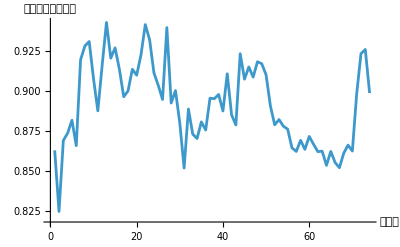

```mathematica
kendallRankR=ListLinePlot[kendalllist[[-74;;]],PlotRange->Full,AxesLabel->{"経過年","前年との相関係数"},ImageSize->400]
```

```mathematica
(*Export[expordoctdir<>"kendallrankr.eps",kendallRankR]*)
```

出版後n年までの累積による順位相関との比較

：n年以降の累積をn年のものにする

```mathematica
Position[targetYears,"2000"]
```

{{68}}

```mathematica
replaceCitedCount[y_,l_,ty_]:=Module[{prepos,pos,lastVal,replist},
prepos=Position[ty,y]//Flatten;
pos=If[prepos=={},1,prepos[[1]]];
lastVal=l[[2,pos]];
replist=Table[n->lastVal,{n,pos,Length[ty]}];
{l[[1]],ReplacePart[l[[2]],replist]}
]
```

```mathematica
replaceCitedCount["2000",top1PcCitedArtCitedCount["1933-2020"][[1]],targetYears]
```

{{1996,10062328},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

：出版後n年以降の累積を打ち切る

```mathematica
cutoffCitedCount[ya_,l_,ty_]:=Module[{fromyear},
fromyear=ToString[ToExpression[ya]+ToExpression[l[[1,1]]]];
If[ToExpression[fromyear]>=2020,l,replaceCitedCount[fromyear,l,ty]]
]
```

```mathematica
cutoffCitedCount[50,top1PcCitedArtCitedCount["1933-2020"][[1]],targetYears]
```

{{1996,10062328},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,3,5,8,11,21,32,54,57,84,121,227,271,450,638,770,832,1027,1208}}

< 出版後3年 >

```mathematica
top1PcCitedArtCitedCountCutoff[3]["1933-2020"]=Map[cutoffCitedCount[3,#,targetYears]&,top1PcCitedArtCitedCount["1933-2020"]]
```

```mathematica
kendalllist3=Table[KendallTau[Transpose[Map[#[[2]]&,top1PcCitedArtCitedCountCutoff[3]["1933-2020"]]][[n-1]],Transpose[Map[#[[2]]&,top1PcCitedArtCitedCountCutoff[3]["1933-2020"]]][[n]]]//N,{n,2,88}]
```

KendallTau::zrvr: 入力されたデータはゼロ分散です．統計値は計算できません．

{Indeterminate,1.,0.998129,0.81535,0.773048,1.,0.999437,0.910384,0.925385,0.799644,0.781259,0.882695,0.832181,0.893262,0.882838,0.933794,0.895207,0.905135,0.866933,0.934907,0.960282,0.960204,0.958355,0.959972,0.973007,0.979342,0.968294,0.966546,0.964426,0.959707,0.979268,0.984701,0.984869,0.9891,0.993038,0.983803,0.981739,0.991155,0.981725,0.988801,0.970841,0.965356,0.946201,0.948488,0.962663,0.960649,0.956666,0.954465,0.959488,0.960993,0.953826,0.953043,0.961614,0.972239,0.949558,0.95587,0.973131,0.9755,0.980024,0.98044,0.982489,0.978379,0.977119,0.966398,0.937134,0.959676,0.949586,0.938932,0.937339,0.933299,0.924899,0.916636,0.932824,0.921697,0.892547,0.899726,0.873534,0.886485,0.902791,0.904679,0.939353,0.936602,0.953899,0.981977,0.987431,0.986076,0.959551}

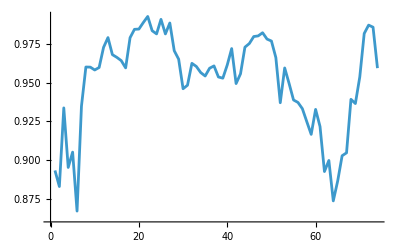

```mathematica
ListLinePlot[kendalllist3[[-74;;]],PlotRange->Full]
```

< 出版後5年 >

```mathematica
top1PcCitedArtCitedCountCutoff[5]["1933-2020"]=Map[cutoffCitedCount[5,#,targetYears]&,top1PcCitedArtCitedCount["1933-2020"]]
```

```mathematica
kendalllist5=Table[KendallTau[Transpose[Map[#[[2]]&,top1PcCitedArtCitedCountCutoff[5]["1933-2020"]]][[n-1]],Transpose[Map[#[[2]]&,top1PcCitedArtCitedCountCutoff[5]["1933-2020"]]][[n]]]//N,{n,2,88}]
```

KendallTau::zrvr: 入力されたデータはゼロ分散です．統計値は計算できません．

{Indeterminate,1.,0.998129,0.49579,0.63216,1.,0.998874,0.91147,0.925592,0.799448,0.7831,0.882061,0.832245,0.889751,0.881845,0.913802,0.897113,0.906074,0.869677,0.931965,0.942108,0.945074,0.950656,0.95471,0.971567,0.974611,0.965671,0.963171,0.964927,0.947553,0.970732,0.979026,0.982601,0.987089,0.993254,0.984295,0.981961,0.989247,0.977772,0.986881,0.971413,0.963154,0.944436,0.949523,0.960488,0.956724,0.957525,0.950348,0.959683,0.959623,0.954419,0.954155,0.960275,0.970588,0.949299,0.955494,0.970527,0.970918,0.975942,0.978969,0.980397,0.976287,0.978238,0.966461,0.938227,0.958146,0.95011,0.938766,0.934498,0.934356,0.924601,0.915225,0.931034,0.915384,0.885524,0.896688,0.877494,0.882159,0.894429,0.89323,0.925526,0.926502,0.942642,0.971894,0.98368,0.983496,0.955733}

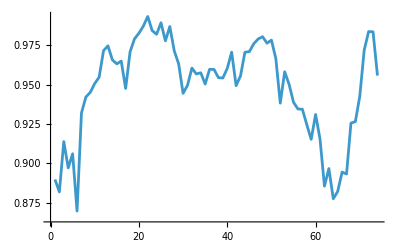

```mathematica
ListLinePlot[kendalllist5[[-74;;]],PlotRange->Full]
```

< 出版後10年 >

```mathematica
top1PcCitedArtCitedCountCutoff[10]["1933-2020"]=Map[cutoffCitedCount[10,#,targetYears]&,top1PcCitedArtCitedCount["1933-2020"]]
```

```mathematica
kendalllist10=Table[KendallTau[Transpose[Map[#[[2]]&,top1PcCitedArtCitedCountCutoff[10]["1933-2020"]]][[n-1]],Transpose[Map[#[[2]]&,top1PcCitedArtCitedCountCutoff[10]["1933-2020"]]][[n]]]//N,{n,2,88}]
```

KendallTau::zrvr: 入力されたデータはゼロ分散です．統計値は計算できません．

{Indeterminate,1.,0.998129,0.49579,0.63216,0.999062,0.997935,0.909069,0.728078,0.631029,0.780963,0.836653,0.798921,0.89025,0.826151,0.88758,0.891618,0.899162,0.864672,0.919861,0.934675,0.933898,0.928263,0.92439,0.954458,0.959433,0.951536,0.959597,0.955866,0.930208,0.957533,0.964516,0.979362,0.979208,0.984135,0.967188,0.97924,0.98632,0.975675,0.986588,0.969447,0.961841,0.939764,0.944701,0.955955,0.954685,0.95606,0.948046,0.954056,0.955405,0.952119,0.953528,0.956723,0.968811,0.947705,0.950155,0.967056,0.966657,0.970247,0.973111,0.976567,0.968937,0.972331,0.956733,0.936846,0.953541,0.944442,0.93364,0.930819,0.927471,0.92135,0.908902,0.920049,0.903943,0.868432,0.886103,0.877719,0.876162,0.882012,0.880107,0.905326,0.908269,0.915726,0.947491,0.967853,0.969781,0.943235}

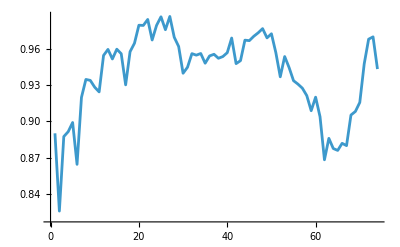

```mathematica
ListLinePlot[kendalllist10[[-74;;]],PlotRange->Full]
```

< 出版後20年 >

```mathematica
top1PcCitedArtCitedCountCutoff[20]["1933-2020"]=Map[cutoffCitedCount[20,#,targetYears]&,top1PcCitedArtCitedCount["1933-2020"]]
```

```mathematica
kendalllist20=Table[KendallTau[Transpose[Map[#[[2]]&,top1PcCitedArtCitedCountCutoff[20]["1933-2020"]]][[n-1]],Transpose[Map[#[[2]]&,top1PcCitedArtCitedCountCutoff[20]["1933-2020"]]][[n]]]//N,{n,2,88}]
```

KendallTau::zrvr: 入力されたデータはゼロ分散です．統計値は計算できません．

{Indeterminate,1.,0.998129,0.49579,0.63216,0.999062,0.997935,0.909069,0.728078,0.631029,0.710815,0.791508,0.755246,0.863018,0.824873,0.869172,0.873767,0.881803,0.865943,0.919497,0.928231,0.931022,0.907458,0.888077,0.916768,0.944986,0.926996,0.933402,0.915522,0.898589,0.903726,0.915071,0.92767,0.945332,0.971439,0.935868,0.941091,0.950758,0.947159,0.974835,0.953176,0.948952,0.921616,0.931733,0.946821,0.946178,0.945414,0.939993,0.946666,0.95348,0.949258,0.949453,0.951514,0.965548,0.942855,0.945868,0.961103,0.952742,0.961217,0.963596,0.966755,0.957339,0.958729,0.941804,0.920715,0.93203,0.918697,0.914144,0.914448,0.907926,0.903574,0.889762,0.908371,0.892472,0.862583,0.883403,0.875618,0.871758,0.879254,0.872357,0.889369,0.895152,0.894571,0.928124,0.948749,0.955134,0.92553}

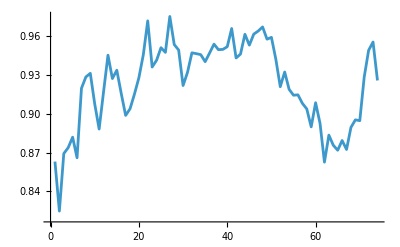

```mathematica
ListLinePlot[kendalllist20[[-74;;]],PlotRange->Full]
```

< 出版後40年 >

```mathematica
top1PcCitedArtCitedCountCutoff[40]["1933-2020"]=Map[cutoffCitedCount[40,#,targetYears]&,top1PcCitedArtCitedCount["1933-2020"]]
```

```mathematica
kendalllist40=Table[KendallTau[Transpose[Map[#[[2]]&,top1PcCitedArtCitedCountCutoff[40]["1933-2020"]]][[n-1]],Transpose[Map[#[[2]]&,top1PcCitedArtCitedCountCutoff[40]["1933-2020"]]][[n]]]//N,{n,2,88}]
```

KendallTau::zrvr: 入力されたデータはゼロ分散です．統計値は計算できません．

{Indeterminate,1.,0.998129,0.49579,0.63216,0.999062,0.997935,0.909069,0.728078,0.631029,0.710815,0.791508,0.755246,0.863018,0.824873,0.869172,0.873767,0.881803,0.865943,0.919497,0.928155,0.930918,0.907636,0.887656,0.916051,0.942813,0.920546,0.926952,0.913534,0.896434,0.900128,0.913615,0.909911,0.922554,0.941483,0.932065,0.911407,0.903611,0.894754,0.939621,0.893482,0.900833,0.880182,0.85193,0.897897,0.881864,0.875211,0.884512,0.88053,0.899257,0.906445,0.915218,0.905926,0.923381,0.903833,0.911244,0.945181,0.925583,0.932665,0.953025,0.955261,0.940516,0.94194,0.923628,0.90122,0.915989,0.899915,0.899616,0.89375,0.890599,0.88826,0.881629,0.896297,0.888716,0.871542,0.878769,0.86833,0.873245,0.869733,0.866617,0.874517,0.879457,0.877483,0.91091,0.936529,0.939163,0.914504}

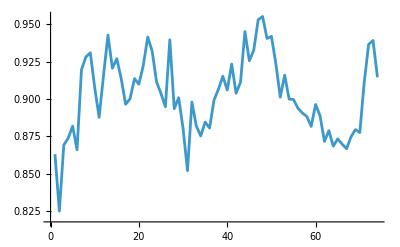

```mathematica
ListLinePlot[kendalllist40[[-74;;]],PlotRange->Full]
```

<比較Plot>

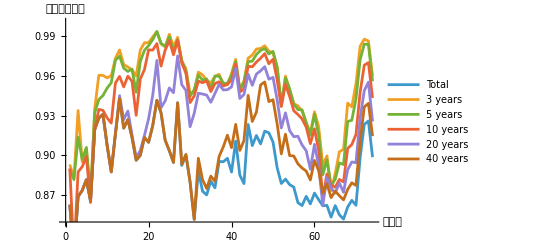

```mathematica
kendallall=ListLinePlot[{kendalllist[[-74;;]],kendalllist3[[-74;;]],kendalllist5[[-74;;]],kendalllist10[[-74;;]],kendalllist20[[-74;;]],kendalllist40[[-74;;]]},PlotLegends->{"Total","3 years","5 years","10 years","20 years","40 years"},PlotRange->{Full, {0.85, 1}},AxesLabel->{"経過年","順位相関係数"},ImageSize->400]
```

```mathematica
(*Export[expordoctdir<>"kendalldiff.eps",kendallall]*)
```

差分

```mathematica
kendalldiff={kendalllist3[[-74;;]]-kendalllist[[-74;;]],kendalllist5[[-74;;]]-kendalllist[[-74;;]],kendalllist10[[-74;;]]-kendalllist[[-74;;]],kendalllist20[[-74;;]]-kendalllist[[-74;;]],kendalllist40[[-74;;]]-kendalllist[[-74;;]]}
```

{{0.0302443,0.0579649,0.0646224,0.0214404,0.0233325,0.000990443,0.0154103,0.0321265,0.0292862,0.0507198,0.0723159,0.0569556,0.036529,0.0477471,0.0395936,0.0508919,0.0632733,0.0791403,0.071086,0.0749585,0.0665462,0.0515546,0.0517375,0.0703317,0.0875441,0.0869715,0.0491796,0.0783106,0.0650497,0.066157,0.0965035,0.0738804,0.0874929,0.0862865,0.073677,0.0837904,0.0654149,0.0585894,0.0551589,0.0740576,0.0614515,0.0643299,0.0769861,0.0498334,0.0680806,0.0649689,0.0717488,0.0641954,0.0613381,0.0670053,0.0756318,0.0581903,0.0774314,0.0714599,0.0626844,0.0727682,0.070942,0.0556221,0.0530133,0.061118,0.0548621,0.0303479,0.0372157,0.0198441,0.0241359,0.0473533,0.0524898,0.0780913,0.0703094,0.0913076,0.0837311,0.0640833,0.0601167,0.0608202},{0.0267329,0.0569719,0.0446304,0.0233469,0.0242713,0.0037339,0.0124686,0.0139525,0.0141563,0.0430209,0.0670538,0.0555156,0.0317982,0.0451243,0.0362193,0.0513922,0.0511191,0.0706038,0.0654111,0.0726904,0.0645346,0.051771,0.05223,0.0705537,0.0856361,0.083018,0.0472598,0.0788827,0.0628474,0.0643913,0.0975389,0.0717052,0.0835677,0.0871453,0.0695604,0.083986,0.0640446,0.0591823,0.056271,0.0727188,0.0598007,0.0640707,0.0766106,0.0472295,0.0634984,0.0608867,0.0702781,0.0621042,0.0592461,0.0681243,0.0756946,0.0592834,0.0759013,0.0719837,0.0625187,0.0699277,0.072,0.0553247,0.0516022,0.0593275,0.0485489,0.0233247,0.0341777,0.0238043,0.0198107,0.038991,0.0410407,0.0642648,0.06021,0.0800499,0.0736489,0.0603318,0.0575372,0.0570019},{0.0272324,0.00127778,0.018408,0.0178514,0.0173595,-0.00127097,0.000363954,0.00651987,0.00297956,0.0206277,0.036734,0.0384075,0.0166196,0.0309899,0.0326453,0.0423314,0.0337745,0.0574052,0.0509008,0.0694513,0.0566542,0.0426517,0.0351226,0.0678332,0.0827087,0.0809216,0.0469674,0.0769172,0.0615348,0.0597194,0.0927161,0.0671718,0.0815288,0.0856807,0.0672578,0.0783582,0.0598265,0.0568821,0.0556437,0.0691664,0.0580241,0.0624769,0.0712714,0.0437586,0.0592367,0.0551911,0.0644206,0.0582742,0.0518961,0.0622169,0.0659665,0.0579019,0.0712961,0.0663158,0.0573928,0.0662484,0.0651143,0.0520738,0.0452799,0.048343,0.0371082,0.00623263,0.0235922,0.0240292,0.0138134,0.0265739,0.0279179,0.0440644,0.0419769,0.0531347,0.0492459,0.044505,0.043822,0.0445048},{0.,0.,0.,0.,0.,0.,0.,0.0000755035,0.000103876,-0.000177593,0.000421349,0.000717369,0.00217278,0.00644948,0.00645009,0.00198794,0.00215494,0.00359834,0.00145563,0.0177594,0.0227775,0.029956,0.00380275,0.029684,0.0471476,0.0524049,0.0352138,0.0606462,0.0486452,0.0415714,0.0797479,0.0580382,0.0730215,0.0750346,0.0592054,0.070969,0.0579016,0.0540211,0.0515689,0.0639576,0.0547608,0.0576262,0.066984,0.0378057,0.0453218,0.0461614,0.0549056,0.0484621,0.0402986,0.0486152,0.0510381,0.041771,0.0497851,0.0405707,0.0378966,0.0498779,0.0455698,0.0342973,0.0261391,0.0366647,0.0256373,0.000384069,0.0208925,0.0219278,0.00940879,0.0238167,0.0201678,0.0281073,0.0288592,0.0319791,0.0298781,0.0254009,0.0291746,0.0267997},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.000952202,0.000526279,0.000138026,-0.0000544006,0.00911454,0.00870775,0.00483136,0.00372449,0.00483307,0.0036781,0.0112079,0.0173343,0.0183693,0.0125936,0.0186043,0.0323608,0.0218839,0.0181636,0.0176092,0.0443339,0.036968,0.0234753,0.0318265,0.0328613,0.0222764,0.0337447,0.0217881,0.0233683,0.0291797,0.0282422,0.0189839,0.0180065,0.024591,0.0218808,0.00934316,0.0162581,0.01464,0.0108958,0.0142952,0.0144277,0.0132551,0.0131643,0.0148917,0.0126641,0.0131814,0.0132038,0.0157735}}

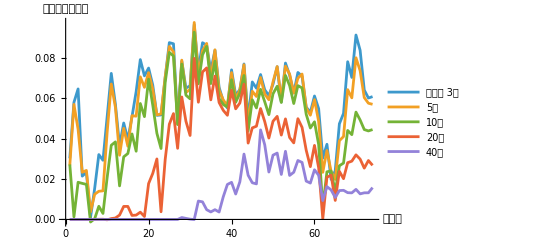

```mathematica
kendalldiffgr=ListLinePlot[kendalldiff,PlotLegends->{"出版後\n3年","5年","10年","20年","40年"},AxesLabel->{"経過年","相関係数の差分"},PlotRange->All]
```

```mathematica
(*Export[expordoctdir<>"kendalldiff.eps",kendalldiffgr]*)
```

## 作図